Sam Dolan, April 2024.
This is a notebook to reconstruct the l-modes of the metric perturbation in Lorenz gauge in the m=0 (axisymmetric) sector, in the frequency domain, for a circular equatorial orbit on Kerr spacetime. For such orbits, the m=0 sector is static (ω=0). This notebook is a companion to metric_reconstruction_calc_radiative.nb.

The code uses the SpinWeightedSphericalHarmonicY function in the SpinWeightedSpheroidalHarmonics package of the Black Hole Perturbation Toolkit. 
It uses pre-calculated input in the directories static/ and completion/ generated by CalcStaticTensorMode.nb and CalcStaticRadialFunctions.nb. 

The metric perturbation has 10 components, but due to symmetries 5 are enough for full knowledge (for m=0).  I use  h_ {ab} projected onto an unnormalised tetrad. I chose the projections in the following order:
  [ h_ {l + l +}, h_ {m + m +}, ρ h_ {l + m +}, Σ h_{m+ m-}, h (the trace) ] .
Note that the fourth component here is Σ h_{m+ m-}  , rather than  Σ Δ h_ {l + l -} in the “radiative” m !=0 notebook. It is straightforward enough to convert using Σ Δ h_ {l + l -}  = Σ^2 h - Σ h_{m+ m-}, but this does involve some mixing of l modes due to the Σ^2 before the h. I do this before exporting.

After projecting onto spherical bases of the appropriate spin-weight, the four components {h_ {l + l +}, h_ {m + m +}, Σ h_ {m + m-}, h} are real for l even, and zero for l odd. The component ρ h_ {l+ m+} is real for l even, and imaginary for l odd.
The spin-weight of each component follows from counting the number of m+ projections and subtracting the number of m- projections.
(There is a subtlety: for some reason I projected ρ h_ {l+ m+} onto a spin minus-one basis. This is fixed before export by introducing a relative minus sign).
Note that I am working with the components after projecting onto the spin-weighted basis. Since Y_{-1} = - Y_{+1} there is an extra minus sign in the symmetries. So (after projecting) ρ* h_ {l+ m -} = - (-1)^l ρ h_ {l+ m +} and ρ h_{l+ m+} = - ρ* h_{l- m-}. See also Eq . (190) in the DDKW paper, arXiv: 2306.16459.

Sections 1 to 6 are necessary to produce output. The later sections are legacy code used for testing. 

The input parameters are read from a file : config/config_ < iConfig > . txt .  There is a naming convention . iConfig should the form XX - YYY - ZZZ, where XX are the first two digits of "a" after the decimal point (i . e . 00 for Schwarzschild, 60 for a = 0.6 M, 99 for a = 0.99 M), YYY are the digits of r0 (with 060 implying r0 = 6.0), and ZZZ are the run numbers, with the first digit typically labelling the internal parameter choices (such as grid size), and the latter two digits indicating the value of ' m' . The numbers 0 ZZ are reserved for testing, whereas the numbers zZZ with z >= 1 are for production runs.

Note that it is necessary to use a high number of digits (‘prec’) to solve accurately at high l. For example, choose parameters prec=100 for lmax=20.

```mathematica
ClearAll["Global`*"];
<<SpinWeightedSpheroidalHarmonics`
mypath=NotebookDirectory[]
```

/Users/sm1srd/Code/KerrLorenz/

```mathematica
iConfig="00-060-000";(* Identifies the parameter file. *)
(* If run as a script, read iConfig from the command line. *)
If[Length[$ScriptCommandLine]==2,
iConfig=$ScriptCommandLine[[2]];
Print["iConfig = " <> ToString[iConfig]];
mypath=Directory[]<>"/";
];
Print[mypath];
```

/Users/sm1srd/Code/KerrLorenz/

```mathematica
runchecks=False; (* Set to true if you want to check the Lorenz gauge condition, etc. This increases the run time. *)
(* Assumptions *)
assum=M>0&&M∈Reals&&a≥ 0&&a<M&&r∈Reals&&r>2M&&r0>2M&&θ∈Reals&&θ>0&&θ<π&&l∈Integers&&l≥2;
assum2=r>rp&&rp>rm&&rm>0&&r∈Reals&&rp∈Reals&&rm∈Reals&&r0∈Reals&&r0>rp&&logp>logm&&logm>0&&logp∈Reals&&logm∈Reals;
Off[ClebschGordan::phy];
```

## 1. Preliminaries

### Import config file

```mathematica
(* Read the parameters from a configuration file *)
filepath=mypath<>"config/";
filen=filepath<>"config"<>ToString[iConfig]<>".txt";
s=Import[filen,"String"];
s1=StringSplit[s,"\n"];
stmp=Map[StringSplit[#,"\t"]&,s1];
(* Handle the case where spaces were used in place of tabs **)
altsplit[s_]:={First[#],Last[#]}&@StringSplit[s," "];
s2=Map[If[Length[#]<2,altsplit[#[[1]]],#]&,stmp];
configparams=Map[{#[[1]],ToExpression[#[[2]]]}&,s2];
GetParam[key_]:=Module[{ls,val},
ls=Select[configparams,#[[1]]==key&];
If[Length[ls]>0,
val=ls[[1]][[2]];
If[ NumericQ[val]&&(!(IntegerQ[val])),val=SetPrecision[val,prec]];
,
val=Null
];
val
];
GetParam[key_,default_]:=If[GetParam[key]===Null,default,GetParam[key]];
```

```mathematica
(* Functions for converting r to z and back again. *)
Getz:=(2*#-rp-rm)/(rp-rm)&;
Getr:=1/2 (rm+rp-rm #+rp #)&;
Getz[Getr[2]]//Simplify
Getr[Getz[6]]//Simplify
(* Function for initialising the numerical parameters. *)
(* NOTE: It seems necessary to specific the input parameters (r0 and a) with high precision, e.g., 6.0`60. *)
SetParams[rr0_,aa_]:=Module[{},
subs1={M->1,a->aa,rp->1+Sqrt[1-aa^2],rm->1-Sqrt[1-aa^2]};
subs2={r0->rr0,z0->Getz[rr0]}/.subs1;
Join[subs1,subs2]
];
rtozsubs={r->Getr[z]}
SetParams[6.0`60,0.9`60]
```

2

6

{r→1/2 (rm+rp-rm z+rp z)}

{M→1,a→0.9,rp→1.435889894354067355223698198385961565913700392523244493689,rm→0.56411010564593264477630180161403843408629960747675550631097,r0→6.,z0→11.470786693528088295360478904893725418781589276927486676027}

```mathematica
iround=1000;
prec=GetParam["prec",50];(* Number of digits to use. This must be read in first. *)
r0val=Round[GetParam["r0"]*iround]/iround;
aval=Round[GetParam["a"]*iround]/iround;
lmax=GetParam["lmax",10];
lplot=GetParam["lplot"];
mypar=SetParams[SetPrecision[r0val,prec],SetPrecision[aval,prec]]
```

{M→1,a→0,rp→2,rm→0,r0→6.,z0→5.}

```mathematica
rgrid=GetParam["rgrid",0]; (* Use a linearly-spaced grid in the variable: 0 = rstar , 1 = r. *)
rstarmin=GetParam["rstmin",SetPrecision[-20.,prec]]; (* If rgrid=1 then these will be interpreted as rmin and rmax, instead of rstarmin and rstarmax. *)
rstarmax=GetParam["rstmax",SetPrecision[rmax,prec]];
nres=GetParam["n",4];  (* Resolution in the r* direction:  dr* = M / n  (or dr = M / n). *)
dformat=ToString@GetParam["dformat","Real64"];
```

### Setup

```mathematica
Δ=r^2-2*M*r+a^2;
Δalt=(r-rp)*(r-rm);
Σ=r^2+a^2*Cos[θ]^2;
λ2hat=Λh/Sqrt[λ];
Lop[n_,S_]:=D[S,θ]+n*Cot[θ]*S;
Y0eq=Lop[1,Lop[0,Y0[θ]]]+λ*Y0[θ];
Y1eq=Lop[0,Lop[1,Y1[θ]]]+λ*Y1[θ];
Y2eq=Lop[-1,Lop[2,Y2[θ]]]+(λ-2)*Y2[θ];
tmp=Solve[Y0eq==0,Y0''[θ]]//First;
Y0subs=Join[tmp,{Y0'''[θ]-> D[Y0''[θ]/.tmp,θ]/.tmp}//Simplify];
tmp=Solve[Y1eq==0,Y1''[θ]]//First;
Y1subs=Join[tmp,{Y1'''[θ]-> D[Y1''[θ]/.tmp,θ]/.tmp}//Simplify];
tmp=Solve[Y2eq==0,Y2''[θ]]//First;
Y2subs=Join[tmp,{Y2'''[θ]-> D[Y2''[θ]/.tmp,θ]/.tmp}//Simplify];
Y2alt1=(1/λ2hat)*Lop[-1,Y1[θ]]/.Y1subs;
Y2alt0=(1/Λh)*Lop[-1,Lop[0,Y0[θ]]]/.Y0subs;
Y0alt1=-1/Sqrt[λ]*Lop[1,Y1[θ]];
Simplify[(Lop[-1,Lop[2,Y2alt1]]+(λ-2)*Y2alt1)/.Y1subs]
Simplify[(Lop[-1,Lop[2,Y2alt0]]+(λ-2)*Y2alt0)/.Y0subs]
Simplify[(Lop[1,Lop[0,Y0alt1]]+λ*Y0alt1)/.Y1subs]
Y2toY1subs={Y2[θ]->Y2alt1,Y2'[θ]->Simplify[ D[Y2alt1,θ]/.Y1subs]}
Y2toY0subs={Y2[θ]->Y2alt0,Y2'[θ]->Simplify[ D[Y2alt0,θ]/.Y0subs]}
Y0toY1subs={Y0[θ]->Y0alt1,Y0'[θ]->Simplify[ D[Y0alt1,θ]/.Y1subs]}
r0subs={r->r0};
Δ0subs={Δ0->r0^2-2*M*r0+a^2};
λsubs={λ->l*(l+1)};
Λhsubs={Λh-> Sqrt[(l-1)*l*(l+1)*(l+2)]};
θsubs={Cos[θ]->cosq,Sin[θ]->sinq,Cos[2θ]-> 2*cosq^2-1,Sin[2θ]->2*cosq*sinq,Csc[θ]->1/sinq,Cot[θ]-> cosq/sinq};

aMsubs={a->Sqrt[rp*rm],M->(rp+rm)/2};
rprmsubs={rp->M+Sqrt[M^2-a^2],rm-> M-Sqrt[M^2-a^2]};
logrepl={Log[(r-rm)/(r-rp)]-> logm-logp,Log[(r-rp)/(r-rm)]-> logp-logm,Log[r-rp]->logp,Log[r-rm]->logm};
reverselogrepl={logp->Log[r-rp],logm-> Log[r-rm]};
```

0

0

0

{Y2[θ]→(√λ (-Cot[θ] Y1[θ]+Y1'[θ]))/Λh,Y2'[θ]→-(√λ ((λ-2 Csc[θ]^2) Y1[θ]+2 Cot[θ] Y1'[θ]))/Λh}

{Y2[θ]→(-λ Y0[θ]-2 Cot[θ] Y0'[θ])/Λh,Y2'[θ]→(2 λ Cot[θ] Y0[θ]+(-λ+2 Cot[θ]^2+2 Csc[θ]^2) Y0'[θ])/Λh}

{Y0[θ]→-(Cot[θ] Y1[θ]+Y1'[θ])/(√λ),Y0'[θ]→√λ Y1[θ]}

```mathematica
(* Metric and principal null tetrad. *)
lvec={(r^2+a^2)/Δ,1,0,a/Δ};
nvec=1/(2*Σ)*{r^2+a^2,-Δ,0,a};
mvec=1/(Sqrt[2]*(r+I*a*Cos[θ]))*{I*a*Sin[θ],0,1,I/Sin[θ]};
mbarvec=1/(Sqrt[2]*(r-I*a*Cos[θ]))*{-I*a*Sin[θ],0,1,-I/Sin[θ]};
gup=Table[-lvec[[i]]*nvec[[j]]-nvec[[i]]*lvec[[j]]+mvec[[i]]*mbarvec[[j]]+mbarvec[[i]]*mvec[[j]],{i,1,4},{j,1,4}];
gdn=Simplify[Inverse[gup]];
lp=lvec;
lm=-2*Σ/Δ*nvec//Simplify;
mp=mvec*Sqrt[2]*(r+I*a*Cos[θ]);
mm=mbarvec*Sqrt[2]*(r-I*a*Cos[θ]);
lpdn=gdn.lp//Simplify;
lmdn=gdn.lm//Simplify;
mpdn=gdn.mp//Simplify;
mmdn=gdn.mm//Simplify;
{lpdn.lm-2*Σ/Δ,mpdn.mm-2*Σ}//Simplify
vecs={lpdn,lmdn,mpdn,mmdn};
tensors=Table[1/2*Table[vecs[[i]][[k]]*vecs[[j]][[l]]+vecs[[i]][[l]]*vecs[[j]][[k]],{k,1,4},{l,1,4}],{i,1,4},{j,1,4}]//Simplify;
(* try a check *)
t0=1/2*Table[(lpdn[[k]]*lmdn[[l]]+lmdn[[k]]*lpdn[[l]]),{k,1,4},{l,1,4}]//Simplify;
t1=tensors[[1,2]];
Simplify[t0-t1]
```

{0,0}

{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Y0pi2subs={Y0[π/2]->SphericalHarmonicY[l,0,π/2,0]}
S0subs={S0->Simplify[Y2alt/.{θ->π/2}]}/.Y0pi2subs;
S0psubs={S0p->Simplify[D[Y2alt,θ]/.{θ->π/2}]}/.{Y0'[π/2]->D[SphericalHarmonicY[l,0,θ,0],θ]/.{θ->π/2}};
numsubs={μ->1,M->1,r0->r0val,l->lval,rp->2,rm->0};
D0subs={D0-> -4*π*μ/(r0^2*ut)};
fixfac=-2;
gravfac=-2*fixfac/(λ*(λ-2));
ABkerr={A-> (EE*(r^2+a^2)-a*LL)/Δ,B->LL-a*EE};
Clear[v];
ELkerr=Simplify[{EE-> (1-2*v^2+atil*v^3)/Sqrt[1-3*v^2+2*atil*v^3],LL-> r*v*(1-2*atil*v^3+atil^2*v^4)/Sqrt[1-3*v^2+2*atil*v^3]}/.{atil->a/M,v-> Sqrt[M/r]},Assumptions-> r0>2*M&&a>0&&a<M&&M>0]
utkerr=Simplify[{ut-> Simplify[(gup.{-EE,0,0,LL})[[1]]/.{θ->π/2}]}/.ELkerr]
chk=Simplify[(ut/.utkerr)-(gup[[1,4]]*LL-gup[[1,1]]*EE)/.{θ->π/2}/.ELkerr]
```

{Y0[π/2]→SphericalHarmonicY[l,0,π/2,0]}

{EE→(-2 M+a √(M/r)+r)/(r √((-3 M+2 a √(M/r)+r)/r)),LL→(-2 a M+a^2 √(M/r)+√(M/r) r^2)/(r √((-3 M+2 a √(M/r)+r)/r))}

{ut→(a √(M/r)+r)/(r √((-3 M+2 a √(M/r)+r)/r))}

0

```mathematica
GetABCD[par_]:=Module[{mysubs1,mysubs2,mysubs3},
mysubs1=ABkerr/.ELkerr/.{r->r0}/.par;
mysubs2=Join[ELkerr,utkerr/.ELkerr]/.{r->r0}/.par;
mysubs3=D0subs/.mysubs2/.{r->r0}/.par/.{μ->1};
Join[mysubs1,mysubs2,mysubs3]
];
```

```mathematica
(* Various replacement rules for the second derivatives. *)
eq=D[Δ*D[hl[r],r],r]-λ*hl[r];
tmp=Solve[eq==0,hl''[r]]//First//Simplify;
hsubs=Join[tmp,{hl'''[r]-> Simplify[D[hl''[r]/.tmp,r]/.tmp]}]
eq=Δ*D[D[DeltaB0[r],r],r]-λ*DeltaB0[r]+2*r*Δ*hl[r];
tmp=Solve[eq==0,DeltaB0''[r]]//First//Simplify;
B0subs=Join[tmp,{DeltaB0'''[r]-> Simplify[D[DeltaB0''[r]/.tmp,r]/.tmp]}]
eq=D[Δ*D[Z[0][r],r],r]-λ*Z[0][r]-hl[r];
tmp=Solve[eq==0,Z[0]''[r]]//First//Simplify;
Z0subs=Join[tmp,{Z[0]'''[r]-> Simplify[D[Z[0]''[r]/.tmp,r]/.tmp]}]
eq=D[Δ*D[R0[r],r],r]-λ*R0[r];
tmp=Solve[eq==0,R0''[r]]//First//Simplify;
R0subs=Join[tmp,{R0'''[r]-> Simplify[D[R0''[r]/.tmp,r]/.tmp]}];
Simplify[D[Δ*D[R0[r],r],r]-λ*R0[r]/.R0subs]
Simplify[D[D[Δ*D[R0[r],r],r]-λ*R0[r],r]/.R0subs]
eq=Δ*P2''[r]-D[Δ,r]*P2'[r]-(λ-2)*P2[r];
P2subs=Solve[eq==0,P2''[r]]//First//Simplify;
Simplify[eq/.P2subs]
```

{hl''[r]→(λ hl[r]+2 (M-r) hl'[r])/(a^2+r (-2 M+r)),hl^(3)[r]→(4 (M-r) λ hl[r]+(8 M^2+a^2 (-2+λ)-2 M r (6+λ)+r^2 (6+λ)) hl'[r])/((a^2+r (-2 M+r))^2)}

{DeltaB0''[r]→(λ DeltaB0[r])/(a^2+r (-2 M+r))-2 r hl[r],DeltaB0^(3)[r]→(2 (M-r) λ DeltaB0[r])/((a^2+r (-2 M+r))^2)-2 hl[r]+(λ DeltaB0'[r])/(a^2-2 M r+r^2)-2 r hl'[r]}

{Z[0]''[r]→(hl[r]+λ Z[0][r]+2 (M-r) Z[0]'[r])/(a^2+r (-2 M+r)),Z[0]^(3)[r]→1/((a^2+r (-2 M+r))^2)(-((-2 M+2 r) (hl[r]+λ Z[0][r]+2 (M-r) Z[0]'[r]))+(a^2+r (-2 M+r)) (hl'[r]-2 Z[0]'[r]+λ Z[0]'[r]+(2 (M-r) (hl[r]+λ Z[0][r]+2 (M-r) Z[0]'[r]))/(a^2+r (-2 M+r))))}

0

0

0

```mathematica
(* Connection and functions for calculating the Lorenz gauge condition. *)
sqrtg=Sin[θ]*Σ;
ρ=r+I*a*Cos[θ];
ρc=r-I*a*Cos[θ];
ρθ=D[ρ,θ]/ρ;
ρcθ=D[ρc,θ]/ρc;
xs={t,r,θ,ϕ};
Γdn=1/2*Table[D[gdn[[k,i]],xs[[j]]]+D[gdn[[i,j]],xs[[k]]]-D[gdn[[j,k]],xs[[i]]],{i,1,4},{j,1,4},{k,1,4}]//Simplify;
Γconn=gup.Γdn//Simplify;
(* assume that ξ has components downstairs *)
GaugeVecToMP[ξ_]:=Module[{part1,part2},
part1=Table[D[ξ[[j]],xs[[k]]]+D[ξ[[k]],xs[[j]]],{j,1,4},{k,1,4}];
part2=-2*ξ.Γconn;
part1+part2
];
GetTrace[h_]:=Module[{},
Sum[h[[j,k]]*gup[[j,k]],{j,1,4},{k,1,4}]
];
GetZDiv[hb_]:=Module[{t0,t1,t2},
t0=Table[Sum[D[hb[[i,j]],xs[[k]]]*gup[[j,k]],{j,1,4},{k,1,4}],{i,1,4}];
t1=Table[Sum[Γconn[[l,i,k]]*hb[[l,j]]*gup[[j,k]],{j,1,4},{k,1,4},{l,1,4}],{i,1,4}];
t2=Table[Sum[Γconn[[l,j,k]]*hb[[i,l]]*gup[[j,k]],{j,1,4},{k,1,4},{l,1,4}],{i,1,4}];
(t0-t1-t2)
];
(* Test the connection has been calculated correctly. *)
(* Metric compatibility condition. *)
dergdn=Table[D[gdn[[i,j]],xs[[k]]],{i,1,4},{j,1,4},{k,1,4}];
connterms=Table[Sum[Γconn[[l,i,k]]*gdn[[j,l]]+Γconn[[l,j,k]]*gdn[[i,l]],{l,1,4}],{i,1,4},{j,1,4},{k,1,4}];
covdn=dergdn-connterms;
Simplify[covdn]
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
(* Make a metric perturbation from the components. *)
(* The argument should be a list of five components. *)
MakeMetricPerturbation[comp_]:=Module[{hlplp=comp[[1]],hmpmp=comp[[2]],ρhlpmp=comp[[3]],Σhmpmm=comp[[4]],trace=comp[[5]],htmp,ρchlpmm},
ρchlpmm=ρhlpmp/.z_Complex:>Conjugate[z];
htmp=hlplp*(tensors[[1,1]]+tensors[[2,2]])*(Δ/(2*Σ))^2
+hmpmp*(tensors[[3,3]]+tensors[[4,4]])*(1/(2*Σ))^2
+ρhlpmp/ρ*(2*tensors[[1,3]]+2*tensors[[2,4]])*(Δ/(2*Σ)^2)
+ρchlpmm/ρc*(2*tensors[[1,4]]+2*tensors[[2,3]])*(Δ/(2*Σ)^2)
+2*(Σhmpmm/Σ)*(tensors[[3,4]])*(1/(2*Σ)^2)
-2*Δ*(Σhmpmm/Σ-Σ*trace)*(tensors[[1,2]])*(1/(2*Σ)^2);
htry=1/2*Table[htmp[[j,k]]+htmp[[k,j]],{j,1,4},{k,1,4}];
htry
];
htohbarcomponent[comp_]:=Simplify[{comp[[1]],comp[[2]],comp[[3]],comp[[4]]-Σ^2*comp[[5]],-comp[[5]]},Assumptions->assum];
Makehbar[comp_]:=MakeMetricPerturbation[htohbarcomponent[comp]];
```

```mathematica
(* Test for consistency. *)
components={H1,H2,H3a+I*H3b,H4,H5};
htmp=MakeMetricPerturbation[components];
Simplify[htmp.lp.lp-H1]
Simplify[htmp.lm.lm-H1]
Simplify[htmp.mp.mp-H2]
Simplify[htmp.mm.mm-H2]
Simplify[ρ*htmp.lp.mp-(H3a+I*H3b)]
Simplify[ρ*htmp.lm.mm-(H3a+I*H3b)]
Simplify[ρc*htmp.lp.mm-(H3a-I*H3b)]
Simplify[ρc*htmp.lm.mp-(H3a-I*H3b)]
Simplify[Σ*htmp.mp.mm-H4]
Simplify[GetTrace[htmp]-H5]
```

0

0

0

«7 more identical outputs»

```mathematica
(* Now set up the vat (a matrix), to be filled later *)
GetEmptyVat[lm_]:=Table[0,{qi,1,5},{ll,0,lm}];
nmax=3;
minl={0,2,1,0,0};
spins={0,-2,-1,0,0};
Vat=GetEmptyVat[lmax]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
(* vat1 should be smaller than, or the same size as, vat2. *)
AddVat[vat1_, vat2_]:=Module[{},
l1=Length[vat1[[1]]]-1;
l2=Length[vat2[[1]]]-1;
newvat=vat2;
For[qi=1,qi<=5,qi++,
For[ll=0,ll<=l1,ll++,
newvat[[qi]][[ll+1]]+=vat1[[qi]][[ll+1]];
];
];
newvat
];
```

```mathematica
(* Restore the coupling coefficients. Note that:
Cc[n][l][k] is zero if |k|>n or k+n odd
 and Cs[n][l][k] is zero if |k|>n+1 or k+n even.
*)
GetCsubs[l_,nmax_]:=Module[{},
mysubs={C0c[0]->KroneckerDelta[k,0],C1c[0]->KroneckerDelta[k,0]};
For[nn=1,nn<=nmax,nn++,
tmp=Table[If[Abs[kk]<=nn&&Mod[nn+kk,2]==0,C0c[nn][l][kk]*KroneckerDelta[k,kk],0],{kk,-nn,nn}];
AppendTo[mysubs,C0c[nn]->Sum[tmp[[kk]],{kk,1,Length[tmp]}]];
tmp=Table[If[Abs[kk]<=nn&&Mod[nn+kk,2]==0,C1c[nn][l][kk]*KroneckerDelta[k,kk],0],{kk,-nn,nn}];
AppendTo[mysubs,C1c[nn]->Sum[tmp[[kk]],{kk,1,Length[tmp]}]];
];
mysubs2={};
For[nn=0,nn<=nmax,nn++,
tmp=Table[If[Abs[kk]<=nn+1&&Mod[nn+kk,2]==1,C0s[nn][l][kk]*KroneckerDelta[k,kk],0],{kk,-nn-1,nn+1}];
AppendTo[mysubs2,C0s[nn]->Sum[tmp[[kk]],{kk,1,Length[tmp]}]];
tmp=Table[If[Abs[kk]<=nn+1&&Mod[nn+kk,2]==1,C1s[nn][l][kk]*KroneckerDelta[k,kk],0],{kk,-nn-1,nn+1}];
AppendTo[mysubs2,C1s[nn]->Sum[tmp[[kk]],{kk,1,Length[tmp]}]];
];
Join[mysubs,mysubs2,{C2c[0]-> KroneckerDelta[k,0]}]
];
```

```mathematica
(* For numerical checks *)
GetRandomIC[fns_]:=Module[{j},
Table[{fns[[j]]'[r]->RandomReal[],fns[[j]][r]->RandomReal[]},{j,1,Length[fns]}]//Flatten
];
```

```mathematica
(* Load the coefficients that were generated in CalcStaticTensorMode.nb *)
cosubs=Get[mypath<>"static/ProjCo.m"];
tracebccoeffs=Get[mypath<>"static/TraceCo.m"];
```

```mathematica
SpinWeightedY[ss_,ll_,θ_]:=If[ll>=Abs[ss],SpinWeightedSphericalHarmonicY[ss,ll,0,θ,0],0];
BrewVat[vat_,lmax_]:=Module[{},
lm=Min[lmax,Length[vat[[1]]]-1];
(* Print[lm]; *)
tmp=Table[Sum[vat[[qi]][[ll+1]]*SpinWeightedY[spins[[qi]],ll,θ],{ll,0,lm}],{qi,1,5}];
tmp/.cosubs/.tracebccoeffs
];
```

```mathematica
(* Visualise the mode couplings *)
Conj[x_]:=x/.z_Complex:>Conjugate[z];
visfn=If[ToString[#]== "0",".",If[ToString[Simplify[Conj[#]-#]]=="0","1",If[ToString[Simplify[Conj[#]+#]]== "0", "i","c"]]]&;
visfn[0]
```

.

## 2. Read metric components

```mathematica
Csubsfn[dl_]:=Join[Flatten[Table[{C0c[nn]->C0c[dl][nn],C0s[nn]-> C0s[dl][nn],C1c[nn]->C1c[dl][nn], C1s[nn]->C1s[dl][nn],C2c[nn]->C2c[dl][nn]},{nn,0,nmax}]],{Y2-> C2c[dl][0]}]
scalarreplacefn[X_]:={R0''[r]-> X''[r],R0'[r]->X'[r],R0[r]->X[r]};
```

### Free scalar mode

```mathematica
filen=mypath<>"static/m0components_free_scalar.m"
hsccomponents=Get[filen]/.{Y2->C2c[0]};
hsccomp=hsccomponents
```

/Users/sm1srd/Code/KerrLorenz/static/m0components_free_scalar.m

{2 C0c[0] R0''[r],2 Λh C2c[0] R0[r],(-2 λ C1c[0] R0[r]+2 (r λ C1c[0]+ⅈ a ((-1+λ) C1c[1]-C1s[0])) R0'[r])/(√λ),-2 (r^2 λ C0c[0]+a^2 (λ C0c[2]-2 C0s[1])) R0[r]+4 r (a^2+r (-2 M+r)) C0c[0] R0'[r],0}

```mathematica
(* Should we consider the l=0 case separately? The formula above breaks down because of λ in denominator. *)
ser=Series[hsccomp,{λ,0,3}] (* The only problematic part is in the third component. *)
myco=Simplify[SpinWeightedSphericalHarmonicY[-1,1,0,θ,0]/Sin[θ]]
component3=2*I*a/Sqrt[4*π]*1/myco*R0'[r]*KroneckerDelta[k,1];
hsc0comp={hsccomp[[1]],hsccomp[[2]],component3,hsccomp[[4]],0}
```

{2 C0c[0] R0''[r],2 Λh C2c[0] R0[r],-(2 ⅈ a (C1c[1]+C1s[0]) R0'[r])/(√λ)+(-2 C1c[0] R0[r]+2 (r C1c[0]+ⅈ a C1c[1]) R0'[r]) √λ+O[λ]^(7/2),(4 a^2 C0s[1] R0[r]+4 r (a^2+r (-2 M+r)) C0c[0] R0'[r])-2 ((r^2 C0c[0]+a^2 C0c[2]) R0[r]) λ+O[λ]^4,0}

-1/2 √(3/(2 π))

{2 C0c[0] R0''[r],2 Λh C2c[0] R0[r],-2 ⅈ √(2/3) a 1,k R0'[r],-2 (r^2 λ C0c[0]+a^2 (λ C0c[2]-2 C0s[1])) R0[r]+4 r (a^2+r (-2 M+r)) C0c[0] R0'[r],0}

```mathematica
(* Note that here we have the coupling coefficients C0c[0], C0c[2],C0s[1], C1c[0], C1c[1], and C1s[0]. *)
PourJug[lm_,l1_,jug_,nm_]:=Module[{},
newvat=GetEmptyVat[lm];
For[kk=-nm-1,kk<=nm+1,kk++,
For[qi=1,qi<=5,qi++,
ind=l1+kk+1;
If[(l1+kk>=minl[[qi]])&&(l1+kk<=lm),
tmp=Simplify[jug[[qi]]/.{k->kk}/.{l->l1}];
newvat=ReplacePart[newvat,{qi,ind}->newvat[[qi]][[ind]]+ tmp]
];
];
];
newvat
];
PourFreeScalar[lm_,l_,Aco_,fn_]:=Module[{nm=2,Rrepl},
If[l==0,tmp=hsc0comp/.GetCsubs[l,nm];,tmp=hsccomp/.GetCsubs[l,nm];];
Rrepl=scalarreplacefn[fn];
jug=Aco*tmp/.{λ->l*(l+1)}/.{Λh->Sqrt[(l-1)*l*(l+1)*(l+2)]}/.Rrepl;
PourJug[lm,l,jug,nm]
];
PourFreeScalar[lm_,l_,Aco_]:=PourFreeScalar[lm,l,Aco,R0[l]];
```

```mathematica
ltry=4;
PourFreeScalar[lmax,ltry,1];
t0=BrewVat[PourFreeScalar[lmax,ltry,1],10];
(* Only when we call "BrewVat" do the spin-weighted spherical harmonics take their explicit form. *)
```

```mathematica
(* Now construct the metric perturbation and verify that it is in Lorenz gauge *)
checks[]:=Module[{},
R0eq=(D[Δ*R0[l]'[r],r]-l*(l+1)*R0[l][r])/.{l->ltry};
tmp=Solve[R0eq==0,R0[ltry]''[r]]//First;
R0subs=Join[{R0[ltry]'''[r]->D[R0[ltry]''[r]/.tmp,r]/.tmp},tmp]//Simplify;
t0=BrewVat[PourFreeScalar[lmax,ltry,1],lmax];
t1=Makehbar[t0];
(* Schwarzschild case *)
t0=Simplify[GetZDiv[t1/.{a->0}]/.R0subs/.{a->0}];
(* Just do a numerical check in the Kerr case *)
numvals={θ->1.3,a->0.9,M->1, r->6.7};
{t0,N[GetZDiv[t1]/.R0subs/.GetRandomIC[{R0[ltry]}]/.numvals,30]}
]
If[runchecks,checks[]]
```

### Even parity

```mathematica
nm=4;
Crepl=GetCsubs[l,nm];
tmp=Get[mypath<>"static/m0components_even_noscalar.m"];
hecomp=Simplify[tmp/.Crepl,Assumptions->assum];
```

```mathematica
GetEvenReplRules[l1_]:=Module[{P2subs,χesubs,χek0subs,P3subs,P4subs},
eq=Δ*P2[l1]''[r]-D[Δ,r]*P2[l1]'[r]-(λ-2)*P2[l1][r];
P2subs=Solve[eq==0,P2[l1]''[r]]//First//Simplify;
eq=D[Δ*χe[l1]'[r],r]-λ*χe[l1][r]-(r*P2[l1]'[r]-2*P2[l1][r]);
χesubs=Solve[eq==0,χe[l1]''[r]]//First//Simplify;
eq=(D[Δ*χek0[l1]'[r],r]-λ*χek0[l1][r]-P2[l1]''[r])/.P2subs;
χek0subs=Solve[eq==0,χek0[l1]''[r]]//First//Simplify;
P3subs=D[P2subs,r]/.P2subs//Simplify;
P4subs=D[P3subs,r]/.P2subs//Simplify;
Join[P4subs,P3subs,P2subs,χesubs,χek0subs]/.λsubs/.{l->l1}
];
GetEvenReplRules[3]
```

{P2[3]^(4)[r]→(120 P2[3][r])/((a^2+r (-2 M+r))^2),P2[3]^(3)[r]→(12 P2[3]'[r])/(a^2+r (-2 M+r)),P2[3]''[r]→(10 P2[3][r]+2 (-M+r) P2[3]'[r])/(a^2+r (-2 M+r)),χe[3]''[r]→(-2 P2[3][r]+12 χe[3][r]+r P2[3]'[r]+2 M χe[3]'[r]-2 r χe[3]'[r])/(a^2+r (-2 M+r)),χek0[3]''[r]→(12 χek0[3][r]+(10 P2[3][r]+2 (-M+r) P2[3]'[r])/(a^2+r (-2 M+r))+2 (M-r) χek0[3]'[r])/(a^2+r (-2 M+r))}

```mathematica
PourEvenParity[lm_,l1_,Aco_]:=Module[{nm=4,P2repl,fnrepl,vat0,vat1,vat2,vat3,vat4,newvat},
P2repl={P2'[r]->P2[l]'[r],P2[r]->P2[l][r]};
jug=hecomp/.P2repl/.λsubs/.Λhsubs/.{l->l1};
(* Now include the scalar part that restores Lorenz gauge. *)
lamsubs={lam[-1]-> (l-2)*(l-1),lam[0]-> l*(l+1),lam[1]->(l+2)*(l+3),λ->l*(l+1),Λh->Sqrt[(l-1)*l*(l+1)*(l+2)]};
scm1fac=-a^2/(λ*Λh)*((λ+2)*C0s[1][l][-2]-2*λ*C0c[2][l][-2])/(λ-lam[-1])/.lamsubs/.{l->l1}; (* P2''[r] *)
scp1fac=-a^2/(λ*Λh)*((λ+2)*C0s[1][l][2]-2*λ*C0c[2][l][2])/(λ-lam[1])/.lamsubs/.{l->l1}; (* P2''[r] *)
sc0fac=-a^2/(λ*Λh)*((λ+2)*C0s[1][l][0]-2*λ*C0c[2][l][0]+2*λ)/.lamsubs/.{l->l1};
χefac=-(Λh/λ)/.lamsubs/.{l->l1};
vat0=PourJug[lm,l1,jug,nm];
vat1=PourFreeScalar[lm,l1-2,scm1fac,P2[l1]''];
vat2=PourFreeScalar[lm,l1+2,scp1fac,P2[l1]''];
vat3=PourFreeScalar[lm,l1,sc0fac,χek0[l1]];
vat4=PourFreeScalar[lm,l1,χefac,χe[l1]];
newvat=vat0+vat1+vat2+vat3+vat4;
Simplify[newvat/.GetEvenReplRules[l1]/.{λ->l1*(l1+1)}]
];
```

```mathematica
checks[]:=Module[{},
ltry=2;
t0=BrewVat[PourEvenParity[lmax,ltry,1],lmax]/.GetEvenReplRules[ltry];
t1=Makehbar[t0];
(* Schwarzschild case *)
t0=Simplify[GetZDiv[t1/.{a->0}]/.GetEvenReplRules[ltry]/.λsubs/.{l->ltry}/.{a->0}];
(* Just do a numerical check in the Kerr case *)
fnvals=GetRandomIC[{χe[ltry],χek0[ltry],P2[ltry]}];
numvals={θ->1.3,a->0.9,M->1, r->6.7};
{t0,N[GetZDiv[t1]/.GetEvenReplRules[ltry]/.λsubs/.{l->ltry}/.fnvals/.numvals,30]}
];
If[runchecks,checks[]]
```

### Odd parity

```mathematica
nm=4;
Crepl=GetCsubs[l,nm];
tmp=Get[mypath<>"static/m0components_odd_noscalar.m"];
hocomp=Simplify[tmp/.Crepl,Assumptions->assum];
```

```mathematica
GetOddReplRules[l1_]:=Module[{P2subs,χocsubs,χossubs},
eq=Δ*P2[l1]''[r]-D[Δ,r]*P2[l1]'[r]-(λ-2)*P2[l1][r];
P2subs=Solve[eq==0,P2[l1]''[r]]//First//Simplify;
eqs=Table[D[Δ*χoc[k][l1]'[r],r]-lamo[k]*χoc[k][l1][r]-P2[l1]'[r]==0,{k,-1,1,2}];
χocsubs=Solve[eqs,Table[χoc[k][l1]''[r],{k,-1,1,2}]]/.P2subs//First//Simplify;
eqs=Table[D[Δ*χos[k][l1]'[r],r]-lamo[k]*χos[k][l1][r]-r*P2[l1]''[r]==0,{k,-1,1,2}]/.P2subs;
χossubs=Solve[eqs,Table[χos[k][l1]''[r],{k,-1,1,2}]]/.P2subs//First//Simplify;
lamodd={lamo[-1]-> (l-1)*l, lamo[1]-> (l+1)*(l+2),λ->l*(l+1),Λh->Sqrt[(l-1)*l*(l+1)*(l+2)]};
Flatten[Join[P2subs,χocsubs,χossubs]]/.lamodd/.{l->l1}
];
GetOddReplRules[3]
```

{P2[3]''[r]→(10 P2[3][r]+2 (-M+r) P2[3]'[r])/(a^2+r (-2 M+r)),χoc[-1][3]''[r]→(P2[3]'[r]+2 (M-r) χoc[-1][3]'[r]+6 χoc[-1][3][r])/(a^2+r (-2 M+r)),χoc[1][3]''[r]→(P2[3]'[r]+2 (M-r) χoc[1][3]'[r]+20 χoc[1][3][r])/(a^2+r (-2 M+r)),χos[-1][3]''[r]→(10 r P2[3][r]+2 r (-M+r) P2[3]'[r]+(a^2+r (-2 M+r)) (2 (M-r) χos[-1][3]'[r]+6 χos[-1][3][r]))/((a^2+r (-2 M+r))^2),χos[1][3]''[r]→(10 r P2[3][r]+2 r (-M+r) P2[3]'[r]+(a^2+r (-2 M+r)) (2 (M-r) χos[1][3]'[r]+20 χos[1][3][r]))/((a^2+r (-2 M+r))^2)}

```mathematica
PourOddParity[lm_,l1_,Aco_]:=Module[{nm=4,P2repl,P2subs,χocsubs,χossubs,vat0,vat1,vat2,vat3,vat4},
P2repl={P2'[r]->P2[l]'[r],P2[r]->P2[l][r]};
jug=hocomp/.P2repl/.λsubs/.Λhsubs/.{l->l1};
(* Now include the scalar part that restores Lorenz gauge. *)
lamodd={lamo[-1]-> (l-1)*l, lamo[1]-> (l+1)*(l+2),λ->l*(l+1),Λh->Sqrt[(l-1)*l*(l+1)*(l+2)]};
scocm1fac=(a*Λh/λ)*C0c[1][l][-1]/.lamodd/.{l->l1}; 
scocp1fac=(a*Λh/λ)*C0c[1][l][1]/.lamodd/.{l->l1}; 
scosm1fac=-(a*Λh/λ^2)*C0s[0][l][-1]/.lamodd/.{l->l1}; 
scosp1fac=-(a*Λh/λ^2)*C0s[0][l][1]/.lamodd/.{l->l1}; 
vat0=PourJug[lm,l1,jug,nm];
vat1=PourFreeScalar[lm,l1-1,scocm1fac,χoc[-1][l1]];
vat2=PourFreeScalar[lm,l1+1,scocp1fac,χoc[1][l1]];
vat3=PourFreeScalar[lm,l1-1,scosm1fac,χos[-1][l1]];
vat4=PourFreeScalar[lm,l1+1,scosp1fac,χos[1][l1]];
(* Apply replacement rules for all the ingredients above *)
Simplify[(vat0+vat1+vat2+vat3+vat4)/.GetOddReplRules[l1]/.lamodd/.{λ->l1*(l1+1)}]
];
```

```mathematica
checks[]:=Module[{},
ltry=3;
t0=BrewVat[PourOddParity[lmax,ltry,1],10]/.GetOddReplRules[ltry];
t1=Makehbar[t0];(* Schwarzschild case *)
t2=Simplify[GetZDiv[t1/.{a->0}]/.λsubs/.{l->ltry}/.{a->0}];
(* Numerical check of the Kerr case *)
fnvals = GetRandomIC[{χoc[-1][ltry],χoc[1][ltry], χos[-1][ltry],χos[1][ltry],P2[ltry]}];
numvals={θ->1.3,a->0.9,M->1, r->6.7};
{t2,N[GetZDiv[t1]/.GetOddReplRules[ltry]/.λsubs/.{l->ltry}/.fnvals/.numvals,30]}
];
If[runchecks,checks[]]
```

### Trace mode

```mathematica
filen=mypath<>"static/m0components_divB.m";
hdivBcomp=Get[filen]
```

{2 C0c[0] (((-2 M+2 r) λ B[r])/((a^2-2 M r+r^2)^2)-(λ B'[r])/(a^2-2 M r+r^2)),-2 Λh C2c[0] B'[r],√λ (-(B[r] (r λ C1c[0]+ⅈ a ((-2+λ) C1c[1]-2 C1s[0])))/(a^2+r (-2 M+r))+2 C1c[0] B'[r]-(r C1c[0]+ⅈ a C1c[1]) B''[r]),-4 r λ B[r] C0c[0]+2 (r^2 λ C0c[0]+a^2 (λ C0c[2]-2 C0s[1])) B'[r],0}

```mathematica
GetTraceReplRules[l1_]:=Module[{X0subs,Z0subs,DeltaB0subs,hlsubs},
eq=D[Δ*X0[l1]'[r],r]-λ*X0[l1][r]-r^2*hl[l1][r];
tmp=Solve[eq==0,X0[l1]''[r]]//First//Simplify;
X0subs=Join[tmp,D[tmp,r]/.tmp]//Simplify;
eq=D[Δ*Z0[l1]'[r],r]-λ*Z0[l1][r]-hl[l1][r];
tmp=Solve[eq==0,Z0[l1]''[r]]//First//Simplify;
Z0subs=Join[tmp,D[tmp,r]/.tmp]//Simplify;
eq=Δ*DeltaB0[l1]''[r]-λ*DeltaB0[l1][r]+2*r*Δ*hl[l1][r];
tmp=Solve[eq==0,DeltaB0[l1]''[r]]//First//Simplify;
DeltaB0subs=Join[tmp,D[tmp,r]/.tmp]//Simplify;
eq=D[Δ*hl[l1]'[r],r]-λ*hl[l1][r];
tmp=Solve[eq==0,hl[l1]''[r]]//First//Simplify;
hlsubs=Join[tmp,D[tmp,r]/.tmp]//Simplify;
Join[X0subs,Z0subs,DeltaB0subs,hlsubs]/.{λ->l1*(l1+1)}
];
GetTraceReplRules[4]
```

{X0[4]''[r]→(r^2 hl[4][r]+20 X0[4][r]+2 (M-r) X0[4]'[r])/(a^2+r (-2 M+r)),X0[4]^(3)[r]→1/((a^2+r (-2 M+r))^2)(-((-2 M+2 r) (r^2 hl[4][r]+20 X0[4][r]+2 (M-r) X0[4]'[r]))+(a^2+r (-2 M+r)) (2 r hl[4][r]+r^2 hl[4]'[r]+18 X0[4]'[r]+(2 (M-r) (r^2 hl[4][r]+20 X0[4][r]+2 (M-r) X0[4]'[r]))/(a^2+r (-2 M+r)))),Z0[4]''[r]→(hl[4][r]+20 Z0[4][r]+2 (M-r) Z0[4]'[r])/(a^2+r (-2 M+r)),Z0[4]^(3)[r]→1/((a^2+r (-2 M+r))^2)(-((-2 M+2 r) (hl[4][r]+20 Z0[4][r]+2 (M-r) Z0[4]'[r]))+(a^2+r (-2 M+r)) (hl[4]'[r]+18 Z0[4]'[r]+(2 (M-r) (hl[4][r]+20 Z0[4][r]+2 (M-r) Z0[4]'[r]))/(a^2+r (-2 M+r)))),DeltaB0[4]''[r]→(20 DeltaB0[4][r])/(a^2+r (-2 M+r))-2 r hl[4][r],DeltaB0[4]^(3)[r]→(40 (M-r) DeltaB0[4][r])/((a^2+r (-2 M+r))^2)-2 hl[4][r]+(20 DeltaB0[4]'[r])/(a^2-2 M r+r^2)-2 r hl[4]'[r],hl[4]''[r]→(20 hl[4][r]+2 (M-r) hl[4]'[r])/(a^2+r (-2 M+r)),hl[4]^(3)[r]→(80 (M-r) hl[4][r]+(18 a^2+8 M^2-52 M r+26 r^2) hl[4]'[r])/((a^2+r (-2 M+r))^2)}

```mathematica
PourDiv[lm_,l_,Aco_,fn_]:=Module[{nm=2,Rrepl},
tmp=hdivBcomp/.GetCsubs[l,nm];
Brepl={B[r]->fn,B'[r]->D[fn,r],B''[r]->D[fn,{r,2}]};
jug=Aco*tmp/.Brepl/.{λ->l*(l+1)}/.{Λh->Sqrt[(l-1)*l*(l+1)*(l+2)]};
PourJug[lm,l,jug,nm]
];
```

```mathematica
PourTraceMode[lm_,l1_,Aco_]:=Module[{nm=4,lamsubs,vat0,vat1,vat2,vat3,vat4,vat5,vat6,vat7,vat8,newvat},
lamsubs={λ->l1*(l1+1),lam[0]->l1*(l1+1),lam[-1]->(l1-2)*(l1-1),lam[1]->(l1+2)*(l1+3)};
(* Scalar parts *)
vat0=PourFreeScalar[lm,l1,1/2,X0[l1]];
vat1=PourFreeScalar[lm,l1,(a^2/2)*C0c[2][l1][0],Z0[l1]];
vat2=PourFreeScalar[lm,l1-2,(a^2/2)*C0c[2][l1][-2]/(λ-lam[-1])/.lamsubs,hl[l1]];
vat3=PourFreeScalar[lm,l1+2,(a^2/2)*C0c[2][l1][2]/(λ-lam[1])/.lamsubs,hl[l1]];
(* Div parts *)
fac=1/(2*l1*(l1+1));
vat4=PourDiv[lm,l1,fac,DeltaB0[l1][r]];
vat5=PourDiv[lm,l1,fac,Δ*X0[l1]'[r]];
fac=a^2/(2*l1*(l1+1));
vat6=PourDiv[lm,l1,fac*bco[l1][0],Δ*Z0[l1]'[r]];
vat7=PourDiv[lm,l1-2,fac*bco[l1][-1]/(λ-lam[-1])/.lamsubs,Δ*hl[l1]'[r]];
vat8=PourDiv[lm,l1+2,fac*bco[l1][1]/(λ-lam[1])/.lamsubs,Δ*hl[l1]'[r]];
(* Don't forget to update the trace itself *)
newvat=vat0+vat1+vat2+vat3+vat4+vat5+vat6+vat7+vat8;
If[l1<=lm,
newvat[[5]][[l1+1]]+=hl[l1][r];
];
(* Apply replacement rules for all the ingredients above *)
Simplify[newvat/.GetTraceReplRules[l1]/.lamsubs/.{λ->l1*(l1+1)}/.{l->l1}]
];
```

```mathematica
checks[]:=Module[{},
ltry=4;
t0=BrewVat[PourTraceMode[lmax,ltry,1],10]/.GetTraceReplRules[ltry];
t1=Makehbar[t0];
(* Schwarzschild case *)
t2=Simplify[GetZDiv[t1/.{a->0}]/.GetTraceReplRules[ltry]/.λsubs/.{l->ltry}/.{a->0}];
(* Numerical check of the Kerr case *)
fnvals = GetRandomIC[{Z0[ltry],X0[ltry],hl[ltry],DeltaB0[ltry]}];
numvals={θ->1.3,a->0.9,M->1, r->6.7};
{t2,N[GetZDiv[t1]/.GetTraceReplRules[ltry]/.λsubs/.{l->ltry}/.fnvals/.numvals,30]}
]
If[runchecks,checks[]]
```

### Completion modes

```mathematica
(* These modes were previously constructed and saved in Jigsaw.nb *)
path=mypath<>"completion/"
hmodeB=Get[path<>"hBmode.m"];
hmodeC=Get[path<>"hCmode.m"];
hmodeD=Get[path<>"hDmode.m"];
hmodeE=Get[path<>"hEmode.m"];
hmodeF=Get[path<>"hFmode.m"];
hmodeAM=Get[path<>"h_angmom_mode.m"];
```

/Users/sm1srd/Code/KerrLorenz/completion/

```mathematica
AppendTrace[mode_,tr_,linsert_]:=Module[{lmax,ll,newmode},
lmax=Length[mode[[1]]]-1;
newmode=Append[mode,Table[0,{ll,0,lmax}]];
newmode[[5]][[linsert+1]]=tr;
newmode
];
```

```mathematica
hcompB=AppendTrace[Transpose[hmodeB],6*Sqrt[4*π],0];
hcompC=AppendTrace[Transpose[hmodeC],0,0];
hcompD=AppendTrace[Transpose[hmodeD],(2+2*(rp+rm)/(rp-rm)*Log[(r-rp)/(r-rm)])*Sqrt[4*π],0];
hcompE=AppendTrace[Transpose[hmodeE],(-4/(rp-rm)*Log[(r-rp)/(r-rm)])*Sqrt[4*π],0];
hcompF=AppendTrace[Transpose[hmodeF],4*a*Sqrt[4*π],0];
hcompAM=AppendTrace[Transpose[hmodeAM],0,0];
```

#### Lorenz gauge checks

```mathematica
(* Check that these modes are in Lorenz gauge *)
checks[]:=Module[{},
t0=BrewVat[hcompB,Length[hcompB[[1]]]-1]//Simplify;
t1=Makehbar[t0];
t2a=Simplify[GetZDiv[t1],Assumptions->assum];

t0=BrewVat[hcompC,Length[hcompC[[1]]]-1]//Simplify;
t1=Makehbar[t0];
t2b=Simplify[GetZDiv[t1],Assumptions->assum];

t0=BrewVat[hcompAM,Length[hcompAM[[1]]]-1]//Simplify;
t1=Makehbar[t0];
t2c=Simplify[GetZDiv[t1],Assumptions->assum];
{t2a,t2b,t2c}
];
If[runchecks,checks[]]
```

```mathematica
(* Numerical checks for the rest. *)
checks[]:=Module[{},
numsubs={rp->1.9,rm->0.3,r->10.0,θ->0.4};

tmp=Simplify[hcompD/.reverselogrepl/.aMsubs,Assumptions->assum2];
t0=Simplify[BrewVat[tmp,Length[hcompD[[1]]]-1],Assumptions->assum2];
t1=Makehbar[t0]/.aMsubs;
t2=GetZDiv[t1]/.aMsubs;
t3a=N[t2/.numsubs];

tmp=Simplify[hcompE/.reverselogrepl/.aMsubs,Assumptions->assum2];
t0=Simplify[BrewVat[tmp,Length[hcompE[[1]]]-1],Assumptions->assum2];
t1=Makehbar[t0]/.aMsubs;
t2=GetZDiv[t1]/.aMsubs;
t3b=N[t2/.numsubs];

tmp=Simplify[hcompF/.reverselogrepl/.aMsubs,Assumptions->assum2];
t0=Simplify[BrewVat[tmp,Length[hcompF[[1]]]-1],Assumptions->assum2];
t1=Makehbar[t0]/.aMsubs;
t2=GetZDiv[t1]/.aMsubs;
t3c=N[t2/.numsubs];
{t3a,t3b,t3c}
];
If[runchecks,checks[]]
```

## 3. Fill Matrix

```mathematica
(* Here I will add all the pieces together, but with coefficients that remain to be determined in the "Jumps" section. *)
Vat=GetEmptyVat[lmax+6];
Dimensions[Vat]
Vat=AddVat[coB*hcompB,Vat];
Vat=AddVat[coC*hcompC,Vat];
Vat=AddVat[coD*hcompD,Vat];
Vat=AddVat[coE*hcompE,Vat];
Vat=AddVat[coF*hcompF,Vat];
Vat=AddVat[coAM*hcompAM,Vat];
Dimensions[Vat]
Monitor[
For[ll=2,ll<=lmax+6,ll++,
If[Mod[ll,2]==0,
R0eq=(D[Δ*R0[ll]'[r],r]-ll*(ll+1)*R0[ll][r]);
R0subs=Solve[R0eq==0,R0[ll]''[r]]//First;
Vat=Vat+Ascal[ll]*PourFreeScalar[lmax+6,ll,1]/.R0subs;
Vat=Vat+Atr[ll]*PourTraceMode[lmax+6,ll,1];
Vat=Vat+Aeven[ll]*PourEvenParity[lmax+6,ll,1];
,
Vat=Vat+Aodd[ll]*PourOddParity[lmax+6,ll,1];
];
];
,ll];
Vat=Vat/.cosubs/.tracebccoeffs
```

{5,27}

{5,27}

{{1},3,{12 coB √π+8 a coF √π-(8 coE √π Log[(r-rp)/(r-rm)])/(-rm+rp)+2 coD √π (2+(2 (rm+rp) Log[(r-rp)/(r-rm)])/(-rm+rp)),0,Atr[2] hl[2][r],0,Atr[4] hl[4][r],0,Atr[6] hl[6][r],0,Atr[8] hl[8][r],0,Atr[10] hl[10][r],0,Atr[12] hl[12][r],0,Atr[14] hl[14][r],0,Atr[16] hl[16][r],0,Atr[18] hl[18][r],0,Atr[20] hl[20][r],0,Atr[22] hl[22][r],0,Atr[24] hl[24][r],0,Atr[26] hl[26][r]}}
 |  |  |  |

```mathematica
(* Jumps. *)
(* The only functions with jumps are P2, P2', hl' (not hl) and R0', R0. All other functions are at least C1 at the particle radius. So make replacements here to get the jumps. *)
haystack={"Z0","X0","DeltaB0","χek0","χe","χoc[-1]","χoc[1]","χos[-1]","χos[1]"}
mysubs1=Flatten[Table[ToExpression[haystack[[jj]]][ll][r]->0,{jj,1,Length[haystack]},{ll,2,lmax+6}]];
mysubs2=Flatten[Table[ToExpression[haystack[[jj]]][ll]'[r]->0,{jj,1,Length[haystack]},{ll,2,lmax+6}]];
VatJumps=Vat/.Table[hl[ll][r]->0,{ll,2,lmax+6}]/.mysubs1/.mysubs2
```

{Z0,X0,DeltaB0,χek0,χe,χoc[-1],χoc[1],χos[-1],χos[1]}

{{1},{0,0,-8 a^2 coB √((2 π)/15)+6+(4 3 (1))/(49 (a^2+1)),0,19,0,1,0,60 √546 Ascal[26] R0[26][r]+(208 √(46/371) a^2 Aeven[24] (1))/(289 (a^2+r (-2 M+r)))-(2 M Aeven[26] (700 r P2[26][r]+(-a^2+r^2) P2[26]'[r]))/(351 (a^2+r (-2 M+r)))},1,{1},{12 coB √π+8 a coF √π-(8 coE √π Log[(r-rp)/(r-rm)])/(-rm+rp)+2 coD √π (2+(2 (rm+rp) Log[(r-rp)/(r-rm)])/(-rm+rp)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}
 |  |  |  |

```mathematica
(* Takes a while to run *)
(*
Map[visfn,VatJumps,{2}]//TableForm 
*)
```

## 4. Jumps

### Calculation functions

```mathematica
(* work out the jumps in the P2 function, in the trace function, and in the monopole. *)
C2=B^2*S0;
C1=2*B*(I*A*S0p+B*S0/r);
C0=2*A*(I*B*2/r+A*I*a/r)*S0p+A^2*(λ-2)*S0;
V0minus4=-(λ-2);
J0=Δ*D0*(C1-2*(r-M)/Δ*C2);
J1=Δ*D0*(C0-V0minus4*C2/Δ);
fac=2*I*Δ*D0*S0p/r;
J0odd=fac*r*A*B;
J1odd=fac*(2*A*B+a*A^2);
fac=D0*S0;
J0even=fac*(-2*(M-a^2/r)*B^2);
J1even=fac*(λ-2)*(Δ*A^2+B^2);
Simplify[(J0-(J0even+J0odd))]
Simplify[J1-(J1even+J1odd)]
(* These are the jumps in the Weyl scalars for each mode. *)
(* don't forget we will still need to multiply by 'gravfac', relating the jump in Weyl scalars to the jump in the metric perturbation. 
Let's do that here. *)
Jumps2={J0o->-I*gravfac* J0odd,J0e->gravfac*J0even,J1o->-I*gravfac*J1odd,J1e->gravfac*J1even}/.{r->r0};
J1h=4*D0*r^2/Δ*Y0/.{r->r0};
Jumpmono={coE->EE,coAM->(LL-a*EE)/M};
```

0

0

```mathematica
SetNumericalJumps[mypar_]:=Module[{},
ABCDsubs=GetABCD[mypar];
P2evensubs=Table[
{P2[ll][r]-> J0e,P2[ll]'[r]-> J1e}/.Jumps2/.λsubs/.{l->ll}/.{S0->SpinWeightedSphericalHarmonicY[-2,ll,0,π/2,0]}/.ABCDsubs/.mypar,{ll,2,lmax+6,2}]//Flatten;
P2oddsubs=Table[
{P2[ll][r]-> J0o,P2[ll]'[r]-> J1o}/.Jumps2/.λsubs/.{l->ll}/.{S0p->D[SpinWeightedSphericalHarmonicY[-2,ll,0,θ,0],θ]/.{θ->π/2}}/.ABCDsubs/.mypar,{ll,3,lmax+5,2}]//Flatten;
hl1subs=Table[
(hl[ll]'[r]-> J1h)/.λsubs/.{l->ll}/.{Y0->SphericalHarmonicY[ll,0,π/2,0]}/.ABCDsubs/.mypar,{ll,2,lmax+6,2}];
Acosubs=Table[{Atr[ll]->1,Aeven[ll]->1,Aodd[ll]->1,R0[ll][r]->Jsc0[ll]/Ascal[ll],R0[ll]'[r]->Jsc1[ll]/Ascal[ll]},{ll,2,lmax+6}]//Flatten;
VatJumps/.P2evensubs/.P2oddsubs/.hl1subs/.Jumpmono/.ABCDsubs/.Acosubs/.reverselogrepl/.{r->r0}/.{z->z0}/.mypar//Simplify
]

SolveJumpEquations[V_]:=Module[{nsol1,checks1},
unknowns0={coB,coC,coD,coF,Jsc0[2],Jsc1[2]};
eqs0={V[[1,1]]==0,V[[4,1]]==0,V[[3,2]]==0,V[[1,3]]==0,V[[2,3]]==0,V[[3,3]]==0};
If[Abs[a/.mypar]<=0.001,
(* In the Schwarzschild case, use the trace equation. *)
eqs0={V[[1,1]]==0,V[[4,1]]==0,V[[3,2]]==0,V[[1,3]]==0,V[[2,3]]==0,V[[5,1]]==0};
];
nsol0=NSolve[eqs0,unknowns0]//First;
(* Now take a larger set of equations, and check a larger set of consistency conditions *)
unknowns1=Join[unknowns0,Table[{Jsc0[ll],Jsc1[ll]},{ll,4,lmax+2,2}]//Flatten,{Jsc0[lmax+4]}];
eqs1=Join[eqs0,Table[{V[[1,ll+1]]==0,V[[2,ll+1]]==0},{ll,4,lmax+2,2}]//Flatten,{V[[4,lmax+2+1]]==0}];
nsol1=NSolve[eqs1,unknowns1]//First;
checks1=Join[{V[[5,1]],V[[4,3]]},Table[{V[[1,ll+1]],V[[2,ll+1]],V[[3,ll]],V[[3,ll+1]],V[[4,ll+1]]},{ll,4,lmax,2}]//Flatten]/.nsol1;
{nsol1,checks1}
];
```

```mathematica
(* Try a numerical calculation *)
VatJumpsNum=SetNumericalJumps[mypar];
{nsol1,checks1}=SolveJumpEquations[VatJumpsNum];
nsol1
checks1
```

{coB→-0.174136462624445156524924726603924319837664251,coC→-1.17868629216549699916642496077262075167253212,coD→0.235702260395515841466948120701616346428278646,coF→0.0320750149549792091393971544723309697582000972928,Jsc0[2]→-0.363286467729495378659064602195200057935002466912,Jsc1[2]→1.71263620501047821367844741034880027312215448687,Jsc0[4]→0.00731099913434041813204598208069888198793704466011,Jsc1[4]→-0.553547077314345944283481500395772493372376238551,Jsc0[6]→-0.000747170698802075289126115597034443481478494603977,Jsc1[6]→0.26673993947234087821802326814129632288782257362,Jsc0[8]→0.000145370474824868944879202043006717808193472072585,Jsc1[8]→-0.156252493226044848753016595940363541263954839161,Jsc0[10]→-0.0000403792094648934408059758381538069145314354621449,Jsc1[10]→0.102476665163404567988308680686054262378707283572,Jsc0[12]→0.0000140821451521288256056728883149556251308575348637,Jsc1[12]→-0.0723379679114640444469693882898820526364821769469,Jsc0[14]→-5.75414923038437076321185916429810693618207650395×10^-6,Jsc1[14]→0.0537725245579419447822148238903658093186215049294,Jsc0[16]→2.64247398536996611974998033755815642730689420512×10^-6,Jsc1[16]→-0.0415336511094778789084816909513569432511448182892,Jsc0[18]→-1.32739895651015450541761682768909300406758925567×10^-6,Jsc1[18]→0.0330425629675625589163591878011423952665390514587,Jsc0[20]→7.15933047774957232874561723244999797962705041612×10^-7,Jsc1[20]→-0.0269119232658606423837547751767795424054180825142,Jsc0[22]→-4.09097329931769443960803523234739843960758559×10^-7,Jsc1[22]→0.0223415649397580883350954076103922931098358092}

{0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.}

### Format

```mathematica
VatJumpsNum=SetNumericalJumps[mypar];
JumpsScalar=SolveJumpEquations[VatJumpsNum][[1]];
```

```mathematica
(* Make a table of the derived unknowns for inclusion in a tex file. *)
header={"l","Jtensor0","Jtensor1","h1","Jsc0","Jsc1"};
nsf=8;
zerosubs=Flatten@Table[{Jsc0[ll]->0,Jsc1[ll]->0,hl[ll]'[r]->0},{ll,1,lmax,2}]
mytable=Table[Join[{ll},Map[NumberForm[#,nsf]&,{P2[ll][r],P2[ll]'[r],hl[ll]'[r],Jsc0[ll],Jsc1[ll]}/.P2evensubs/.P2oddsubs/.hl1subs/.JumpsScalar/.zerosubs]],{ll,2,lmax}];
mygrid=Grid[Join[{header},mytable],Frame->All,Alignment->Right]
TeXForm[mygrid]
```

{Jsc0[1]→0,Jsc1[1]→0,hl[1]'[r]→0,Jsc0[3]→0,Jsc1[3]→0,hl[3]'[r]→0,Jsc0[5]→0,Jsc1[5]→0,hl[5]'[r]→0,Jsc0[7]→0,Jsc1[7]→0,hl[7]'[r]→0,Jsc0[9]→0,Jsc1[9]→0,hl[9]'[r]→0,Jsc0[11]→0,Jsc1[11]→0,hl[11]'[r]→0,Jsc0[13]→0,Jsc1[13]→0,hl[13]'[r]→0,Jsc0[15]→0,Jsc1[15]→0,hl[15]'[r]→0,Jsc0[17]→0,Jsc1[17]→0,hl[17]'[r]→0,Jsc0[19]→0,Jsc1[19]→0,hl[19]'[r]→0}

l | Jtensor0 | Jtensor1 | h1 | Jsc0 | Jsc1
2 | 0.38137135 | -3.8137135 | 0.46708260 | -0.36328647 | 1.7126362
3 | 1.9772550 | 0.65908502 | 0 | 0 | 0
4 | -0.022018485 | 0.99083182 | -0.46999280 | 0.0073109991 | -0.55354708
5 | -0.46841522 | -0.15613841 | 0 | 0 | 0
6 | 0.0045937328 | -0.45937328 | 0.47071754 | -0.00074717070 | 0.26673994
7 | 0.18018103 | 0.060060342 | 0 | 0 | 0
8 | -0.0015164493 | 0.26537863 | -0.47100034 | 0.00014537047 | -0.15625249
9 | -0.087713526 | -0.029237842 | 0 | 0 | 0
10 | 0.00064037876 | -0.17290227 | 0.47113885 | -0.000040379209 | 0.10247667
11 | 0.049172116 | 0.016390705 | 0 | 0 | 0
12 | -0.00031586195 | 0.12160685 | -0.47121674 | 0.000014082145 | -0.072337968
13 | -0.030296203 | -0.010098734 | 0 | 0 | 0
14 | 0.00017345242 | -0.090195257 | 0.47126482 | -5.7541492×10^-6 | 0.053772525
15 | 0.019975074 | 0.0066583579 | 0 | 0 | 0
16 | -0.00010305858 | 0.069564542 | -0.47129656 | 2.6424740×10^-6 | -0.041533651
17 | -0.013859798 | -0.0046199328 | 0 | 0 | 0
18 | 0.000065043385 | -0.055286877 | 0.47131860 | -1.3273990×10^-6 | 0.033042563
19 | 0.010007692 | 0.0033358973 | 0 | 0 | 0
20 | -0.000043058626 | 0.044996264 | -0.47133452 | 7.1593305×10^-7 | -0.026911923

\begin{array}{rrrrrr}
 \text{l} & \text{Jtensor0} & \text{Jtensor1} & \text{h1} & \text{Jsc0} & \text{Jsc1} \\
 2 & 0.38137135 & -3.8137135 & 0.46708260 & -0.36328647 & 1.7126362 \\
 3 & 1.9772550 & 0.65908502 & 0 & 0 & 0 \\
 4 & -0.022018485 & 0.99083182 & -0.46999280 & 0.0073109991 & -0.55354708 \\
 5 & -0.46841522 & -0.15613841 & 0 & 0 & 0 \\
 6 & 0.0045937328 & -0.45937328 & 0.47071754 & -0.00074717070 & 0.26673994 \\
 7 & 0.18018103 & 0.060060342 & 0 & 0 & 0 \\
 8 & -0.0015164493 & 0.26537863 & -0.47100034 & 0.00014537047 & -0.15625249 \\
 9 & -0.087713526 & -0.029237842 & 0 & 0 & 0 \\
 10 & 0.00064037876 & -0.17290227 & 0.47113885 & -0.000040379209 & 0.10247667 \\
 11 & 0.049172116 & 0.016390705 & 0 & 0 & 0 \\
 12 & -0.00031586195 & 0.12160685 & -0.47121674 & 0.000014082145 & -0.072337968 \\
 13 & -0.030296203 & -0.010098734 & 0 & 0 & 0 \\
 14 & 0.00017345242 & -0.090195257 & 0.47126482 & -5.7541492\times 10^{-6} & 0.053772525 \\
 15 & 0.019975074 & 0.0066583579 & 0 & 0 & 0 \\
 16 & -0.00010305858 & 0.069564542 & -0.47129656 & 2.6424740\times 10^{-6} & -0.041533651 \\
 17 & -0.013859798 & -0.0046199328 & 0 & 0 & 0 \\
 18 & 0.000065043385 & -0.055286877 & 0.47131860 & -1.3273990\times 10^{-6} & 0.033042563 \\
 19 & 0.010007692 & 0.0033358973 & 0 & 0 & 0 \\
 20 & -0.000043058626 & 0.044996264 & -0.47133452 & 7.1593305\times 10^{-7} & -0.026911923 \\
\end{array}

```mathematica
terms={coB,coC,coD,coF,coE,coAM};
mytable=Table[{ToString[terms[[kk]]],NumberForm[terms[[kk]]/.Jumpmono/.JumpsScalar/.GetABCD[mypar]/.mypar,nsf]},{kk,1,Length[terms]}];
mygrid=Grid[mytable,Frame->All,Alignment->Right]
TeXForm[mygrid]
```

coB | -0.17413646
coC | -1.1786863
coD | 0.23570226
coF | 0.032075015
coE | 0.94280904
coAM | 3.4641016

\begin{array}{rr}
 \text{coB} & -0.17413646 \\
 \text{coC} & -1.1786863 \\
 \text{coD} & 0.23570226 \\
 \text{coF} & 0.032075015 \\
 \text{coE} & 0.94280904 \\
 \text{coAM} & 3.4641016 \\
\end{array}

### Export

```mathematica
mytable=Table[Join[{ll},{P2[ll][r],P2[ll]'[r],hl[ll]'[r],Jsc0[ll],Jsc1[ll]}/.P2evensubs/.P2oddsubs/.hl1subs/.JumpsScalar/.zerosubs],{ll,0,lmax}];
Export[mypath<>"data/jumps_"<>ToString[iConfig]<>".mx",mytable]
mytable=Table[{ToString[terms[[kk]]],terms[[kk]]/.Jumpmono/.JumpsScalar/.GetABCD[mypar]/.mypar},{kk,1,Length[terms]}];
Export[mypath<>"data/jumps_completion_"<>ToString[iConfig]<>".mx",mytable]
```

/Users/sm1srd/Code/KerrLorenz/data/jumps_-boson-00-060-000.mx

/Users/sm1srd/Code/KerrLorenz/data/jumps_completion_-boson-00-060-000.mx

## 5. Import radial functions

```mathematica
(* Import the scalar functions *)
scalarfns=Get[mypath<>"static/static_radial_functions.m"];
{Length[scalarfns],Length[scalarfns[[1]]]}
```

{9,25}

```mathematica
GetSmoothedFunction[fnname_,ll_,Bco_,par_]:=Module[{Zint,Zext,r0,Asol},
ind=Position[haystack,fnname][[1,1]];
fn=scalarfns[[ind]][[ll-1]];
X0jump=Bco[[2]]*fn[[2]]-Bco[[1]]*fn[[1]]/.{z->z0}/.par;
X1jump=D[Bco[[2]]*fn[[2]]-Bco[[1]]*fn[[1]],z]/.{z->z0}/.par;
Asol=Solve[{X0jump==0,X1jump==0},{Ain,Aup},WorkingPrecision->prec]//First;
{Bco[[1]]*fn[[1]],Bco[[2]]*fn[[2]]}/.Asol/.par
];
MakeCompositeFunction[fns_,par_]:=((HeavisideTheta[z0-z]*fns[[1]]+HeavisideTheta[z-z0]*fns[[2]])/.par);
GetSmoothedFunction["X0",3,{1,2},mypar]
```

{(4 (2033-9750 z^2+666 z^3+4725 z^4+1050 z^5-13688.2453528275586336507968125396861 z (-3+5 z^2))+3264 z (-3+5 z^2) Log[1+z])/30240,1/30240(-1260 (1.52894636349500284387556950111528118×10^7-26 z-5.73354886310626066453338562918230443×10^7 z^2+30 z^3+3 (1-6 z^2+5 z^4-1.91118295436875355484446187639410148×10^6 z (-3+5 z^2)) Log[-1+z]-3 (1-6 z^2+5 z^4-1.91118295436875355484446187639410148×10^6 z (-3+5 z^2)) Log[1+z])+8 (-414 z+944 z^2+690 z^3-1050 z^4-46 z (-3+5 z^2) (3+π^2+3 Log[2]^2)-1.50505657656539342444001372766035491×10^8 (8-30 z^2+(9 z-15 z^3) Log[(-1+z)/(1+z)])-184 Log[1+z]-564 z Log[1+z]+690 z^2 Log[1+z]+733 z^3 Log[1+z]+525 z^5 Log[1+z]+Log[-1+z] (-184+564 z+690 z^2-733 z^3-525 z^5-276 z (-3+5 z^2) Log[(1+z)/2]+138 z (-3+5 z^2) Log[1+z])-276 z (-3+5 z^2) PolyLog[2,(1-z)/2])-720 (1.33782806805812748839112331347587103×10^7-3 π^2 z-5.01685505521797808146671242553451638×10^7 z^2+5 π^2 z^3-9 z Log[2]^2+15 z^3 Log[2]^2+4 Log[1+z]-1.50505507656539342444001372766035491×10^7 z Log[1+z]-15 z^2 Log[1+z]+2.50842452760898904073335621276725819×10^7 z^3 Log[1+z]+Log[-1+z] (4+1.50505632423031843234157067867817354×10^7 z-15 z^2-2.50842660705053072056928446446362256×10^7 z^3+3 z (-3+5 z^2) Log[1+z])+6 z (-3+5 z^2) PolyLog[2,(1-z)/2]))}

Plot::precw: The precision of the argument function (Re[«1»]) is less than WorkingPrecision (50.).

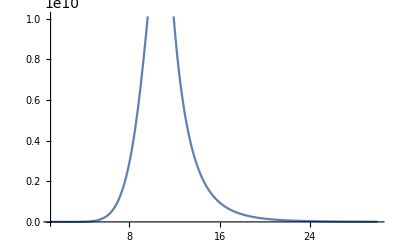

```mathematica
ltry=8;
partry=SetParams[SetPrecision[6,prec],SetPrecision[9/10,prec]];
{"Z0","X0","DeltaB0","χek0","χe","χoc[-1]","χoc[1]","χos[-1]","χos[1]"};
fns=GetSmoothedFunction["DeltaB0",ltry,{1,1},partry];
myf=MakeCompositeFunction[fns,partry];
Plot[Re[myf],{z,SetPrecision[1.01,prec],SetPrecision[30,prec]},WorkingPrecision->prec]
```

```mathematica
Gethlfunction[ll_]:=Module[{},
{LegendreP[ll,z],LegendreQ[ll,0,3,z]}
];
GetP2function[ll_]:=Module[{prefac},
prefac=Δ^2*D[Getz[r],r]^2/.{r->Getr[z]}/.aMsubs//Simplify;
prefac*{D[LegendreP[ll,z],{z,2}], D[LegendreQ[ll,0,3,z],{z,2}]}
]
(* Check these satisfy the ODEs. *)
ltry=4;
Ztry=Gethlfunction[ltry][[2]];
Simplify[D[(z^2-1)*D[Ztry,z],z]-ltry*(ltry+1)*Ztry]
Ztry=GetP2function[ltry][[2]];
Simplify[(z^2-1)*D[D[Ztry,z],z]-2*z*D[Ztry,z]-(ltry-1)*(ltry+2)*Ztry]
```

0

0

## 6. Numerical calculation and export

### Functions

```mathematica
CalculateLeftRightCoeffs[nsol1_,mypar_]:=Module[{Ainrepl,Aoutrepl,Ain0subs,Aout0subs},
(* Now we need to work out the coefficients from the jumps. *)
dzdr=D[Getz[r],r];
ABCDsubs=GetABCD[mypar];
For[ll=2,ll<=lmax+6,ll++,
Ainsubs[ll]={};
Aoutsubs[ll]={};
Print[ll];
If[Mod[ll,2]==0,
(* spin 2 even *)
jumps= {J0e,J1e}/.Jumps2/.λsubs/.{l->ll}/.{S0->SpinWeightedSphericalHarmonicY[-2,ll,0,π/2,0]}/.ABCDsubs/.mypar;
fns=GetP2function[ll];
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout},WorkingPrecision->prec]//First;
AppendTo[Ainsubs[ll],Aeven[ll]-> Ain/.Asol];
AppendTo[Aoutsubs[ll],Aeven[ll]-> Aout/.Asol];
(* trace *)
fns=Gethlfunction[ll];
jumps={0,J1h}/.λsubs/.{l->ll}/.{Y0->SphericalHarmonicY[ll,0,π/2,0]}/.ABCDsubs/.mypar;
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout},WorkingPrecision->prec]//First;
AppendTo[Ainsubs[ll],(Atr[ll]->Ain)/.Asol];
AppendTo[Aoutsubs[ll],(Atr[ll]->Aout)/.Asol];
(* scalar *)
fns=Gethlfunction[ll];
jumps={Jsc0[ll],Jsc1[ll]}/.nsol1;
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout},WorkingPrecision->prec]//First;
AppendTo[Ainsubs[ll],(Ascal[ll]->Ain)/.Asol];
AppendTo[Aoutsubs[ll],(Ascal[ll]->Aout)/.Asol];
,
(* spin 2 odd *)
jumps={J0o,J1o}/.Jumps2/.λsubs/.{l->ll}/.{S0p->D[SpinWeightedSphericalHarmonicY[-2,ll,0,θ,0],θ]/.{θ->π/2}}/.ABCDsubs/.mypar;
fns=GetP2function[ll];
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout},WorkingPrecision->prec]//First;
AppendTo[Ainsubs[ll],Aodd[ll]-> Ain/.Asol];
AppendTo[Aoutsubs[ll],Aodd[ll]-> Aout/.Asol];
];
];
(* Now we need the jump conditions for the completion pieces *)
(* The following generates a solution with the right mass and angular momentum, but which is irregular at infinity due to the D solution,
and irregular at the horizon, due to the F solution. *)
(*
Ain0subs={coB->-(coB/.nsol1),coC->0,coD->0,coE->0,coAM->0,coF->-(coF/.nsol1)};(* minus signs because on the inside. *)
Aout0subs={coB->0,coC->(coC/.nsol1),coD->(coD/.nsol1),coE-> (coE/.Jumpmono/.ABCDsubs),coAM->(coAM/.Jumpmono/.ABCDsubs/.mypar),coF->0};
*)

(* Alternatively, add homogeneous modes to construct the Berndtson-plus solution, which is regular at the horizon and at infinity,
 and which is zero in the tr,tθ,rϕ,θϕ components. It has the wrong mass AND the wrong angular momentum. *)
(* It has zero in the D component in the exterior. *)
Ain0subs={coB->-(coB/.nsol1),coC->((-2*M*rp^2*coD-(a/6)*(rm^3+rm^2*rp+5*rm*rp^2-7*rp^3)*coF)/.nsol1),coD->(-coD/.nsol1),coE->(-M*coD/.nsol1),coAM->((-a*coD-rp*(rp-rm)^2/(rp+rm)*coF)/.nsol1),coF->-(coF/.nsol1)}/.mypar;(* minus signs in the expressions below because now on the inside. *)
Aout0subs={coB->0,coC->((coC-2*M*rp^2*coD-(a/6)*(rm^3+rm^2*rp+5*rm*rp^2-7*rp^3)*coF)/.nsol1),coD->0,coE-> ((coE-M*coD/.nsol1)/.Jumpmono/.ABCDsubs),coAM->((coAM-a*coD-rp*(rp-rm)^2/(rp+rm)*coF)/.nsol1/.Jumpmono/.ABCDsubs/.mypar),coF->0}/.mypar;

Ainrepl=Join[Ain0subs,Table[Ainsubs[ll],{ll,2,lmax+4}]//Flatten];
Aoutrepl=Join[Aout0subs,Table[Aoutsubs[ll],{ll,2,lmax+4}]//Flatten];
{Ainrepl,Aoutrepl,Ain0subs,Aout0subs}
];
```

```mathematica
GetAllRadialFunctions[{Ainrepl_,Aoutrepl_},mypar_]:=Module[{fnsin,fnsout},
fnsin={};
fnsout={};
For[ll=2,ll<=lmax+4,ll++,
If[Mod[ll,2]==0,
(* Trace functions *)
fnnames={"Z0","X0","DeltaB0"};
ampls={Atr[ll]/.Ainrepl,Atr[ll]/.Aoutrepl};
dzdr=D[Getz[r],r];
For[fnct=1,fnct<=Length[fnnames],fnct++,
fnname=fnnames[[fnct]];
fns=GetSmoothedFunction[fnname,ll,ampls,mypar];
AppendTo[fnsin,ToExpression[fnname][ll][r]->fns[[1]]];
AppendTo[fnsin,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[1]],z]/.mypar];
AppendTo[fnsout,ToExpression[fnname][ll][r]->fns[[2]]];
AppendTo[fnsout,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[2]],z]/.mypar];
];
AppendTo[fnsin,hl[ll][r]->Atr[ll]*Gethlfunction[ll][[1]]/.Ainrepl];
AppendTo[fnsin,hl[ll]'[r]->Atr[ll]*dzdr*D[Gethlfunction[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,hl[ll][r]->Atr[ll]*Gethlfunction[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,hl[ll]'[r]->Atr[ll]*dzdr*D[Gethlfunction[ll][[2]],z]/.Aoutrepl];
(* Even parity functions *)
fnnames={"χek0","χe"};
ampls={Aeven[ll]/.Ainrepl,Aeven[ll]/.Aoutrepl};
dzdr=D[Getz[r],r];
For[fnct=1,fnct<=Length[fnnames],fnct++,
fnname=fnnames[[fnct]];
fns=GetSmoothedFunction[fnname,ll,ampls,mypar];
AppendTo[fnsin,ToExpression[fnname][ll][r]->fns[[1]]];
AppendTo[fnsin,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[1]],z]/.mypar];
AppendTo[fnsout,ToExpression[fnname][ll][r]->fns[[2]]];
AppendTo[fnsout,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[2]],z]/.mypar];
];
AppendTo[fnsin,P2[ll][r]->Aeven[ll]*GetP2function[ll][[1]]/.Ainrepl];
AppendTo[fnsin,P2[ll]'[r]->Aeven[ll]*dzdr*D[GetP2function[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,P2[ll][r]->Aeven[ll]*GetP2function[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,P2[ll]'[r]->Aeven[ll]*dzdr*D[GetP2function[ll][[2]],z]/.Aoutrepl];
(* Free scalar functions *)
AppendTo[fnsin,R0[ll][r]->Ascal[ll]*Gethlfunction[ll][[1]]/.Ainrepl];
AppendTo[fnsin,R0[ll]'[r]->Ascal[ll]*dzdr*D[Gethlfunction[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,R0[ll][r]->Ascal[ll]*Gethlfunction[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,R0[ll]'[r]->Ascal[ll]*dzdr*D[Gethlfunction[ll][[2]],z]/.Aoutrepl];
,
(* Odd parity functions *)
fnnames={"χoc[-1]","χoc[1]","χos[-1]","χos[1]"};
ampls={Aodd[ll]/.Ainrepl,Aodd[ll]/.Aoutrepl};
dzdr=D[Getz[r],r];
For[fnct=1,fnct<=Length[fnnames],fnct++,
fnname=fnnames[[fnct]];
fns=GetSmoothedFunction[fnname,ll,ampls,mypar];
AppendTo[fnsin,ToExpression[fnname][ll][r]->fns[[1]]];
AppendTo[fnsin,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[1]],z]/.mypar];
AppendTo[fnsout,ToExpression[fnname][ll][r]->fns[[2]]];
AppendTo[fnsout,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[2]],z]/.mypar];
];
AppendTo[fnsin,P2[ll][r]->Aodd[ll]*GetP2function[ll][[1]]/.Ainrepl];
AppendTo[fnsin,P2[ll]'[r]->Aodd[ll]*dzdr*D[GetP2function[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,P2[ll][r]->Aodd[ll]*GetP2function[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,P2[ll]'[r]->Aodd[ll]*dzdr*D[GetP2function[ll][[2]],z]/.Aoutrepl];
];
];
{fnsin,fnsout}
];
```

### Calculate

```mathematica
VatJumpsNum=SetNumericalJumps[mypar];
{nsol1,checks1}=SolveJumpEquations[VatJumpsNum];
checks1 (* Excellent, the consistency equations are clearly satisfied. *)
```

{0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.}

```mathematica
(* We lose accuracy at high ell. The simplest way to deal with this is by increasing "prec". *)
{Ainrepl,Aoutrepl,Ain0subs,Aout0subs}=CalculateLeftRightCoeffs[nsol1,mypar];
{fnsin,fnsout}=GetAllRadialFunctions[{Ainrepl,Aoutrepl},mypar];
```

2

3

4

5

6

7

8

9

10

11

12

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{2.49376467062985563588932×10^-10,-4.52843546291136×10^14,0.000315861951025864412610291},{-5.58660936680914002183661×10^-10,-1.29759637735728×10^15,-0.121606851144957798854962}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{5.69176770467217448712033×10^-14,-1.43457011569×10^11,0},{-1.51152850833580628296445×10^-13,-3.5108127093×10^11,0.471216741080534762417026}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{5.69176770467217448712033×10^-14,-1.43457011569×10^11,-0.0000140821451521288256056729},{-1.51152850833580628296445×10^-13,-3.5108127093×10^11,0.0723379679114640444469694}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

13

14

15

16

17

18

19

20

21

22

23

24

25

Solve::svars: Equations may not give solutions for all "solve" variables.

26

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.05,0.05,0.005},{0.2,0.2,-0.0003}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-0.2,0.2,0.06},{1.,0.9,0.002}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{2.×10^-6,2.4×10^-8,0.00096},{-9.4×10^-6,1.1×10^-7,-0.003}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

### Extend Vat to include Σ Δ h_{l+ l-}

For the m!=0 modes, I have been exporting Σ Δ h_{l+l-} rather than Σ h_{m+m-}.
The two components are related by Σ Δ h_{l+l-} = Σ^2 h - Σ h_{m+m-}. 
A slight complication is that the Σ^2 factor in front of the trace (h) leads to coupling between l modes in the range (l-4, l+4). 
Here I handle this by extending “Vat” to include a sixth column for the l-modes of Σ Δ h_{l+ l-}.

```mathematica
ExtendVat[V_]:=Module[{},
dim=Dimensions[V];
row=Table[SetPrecision[0,prec],{ll,0,dim[[2]]-1}];
For[ll=0,ll<=lmax+6,ll++,
If[ll<=lmax&&Mod[ll,2]==0,
row[[ll+1]]=r^4*Vat[[5,ll+1]]-Vat[[4,ll+1]]
+2*a^2*r^2*Sum[C0c[2][ll][kk]*Vat[[5,ll+kk+1]],{kk,-Min[ll,2],2,2}]
+a^4*Sum[C0c[4][ll][kk]*Vat[[5,ll+kk+1]],{kk,-Min[ll,4],4,2}];
;
];
];
V2=Append[Vat,row/.cosubs];
V2
]
```

```mathematica
ToTenComponents[in_,ll_]:=Module[{fac=-1,out},
(* For m=0, there are five independent degrees of freedom. Above, I have extended the Vat to six rows. 
However, we want output data in the same format as for the m != 0 modes, for which we use a set of 10 metric components. Here I apply the symmetries of the MP to build the set of 10.
*)
(* Here fac = -1 is because, for some reason when I first wrote the code, I projected the ρ h_{l+ m+} component onto the spin = -1 harmonic . This can be easily recitified here, since Y_{-1} = - Y_{+1} for m=0. *)
If[Mod[ll,2]==0,
out={Re[in[[1]]],Re[in[[1]]],Re[in[[2]]],Re[in[[2]]],fac*Re[in[[3]]],-fac*Re[in[[3]]],fac*Re[in[[3]]],-fac*Re[in[[3]]],Re[in[[6]]],Re[in[[5]]]};
,
out={0,0,0,0,fac*I*Im[in[[3]]],fac*I*Im[in[[3]]],-fac*I*Im[in[[3]]],-fac*I*Im[in[[3]]],0,0};
];
out
];
```

### Set up grid

```mathematica
TortoiseCoord[r_]:=
r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]-rm*Log[(r-rm)/2])/.mypar;
InvTortoise[x_?NumericQ]:=r/.FindRoot[TortoiseCoord[r]-x,{r,(rp+SetPrecision[10^(-5),prec])/.mypar},WorkingPrecision->prec-2];
InvTortoise[TortoiseCoord[6]]
(* Note that the coefficients have been absorbed into the definition of the functions, as is required for the smoothing process. So now we set the coefficients to unity. *)
Getznum[rr_?NumericQ]=(2*rr-rp-rm)/(rp-rm)/.mypar;
Aunitysubs=Table[{Atr[ll]->1,Aeven[ll]->1,Aodd[ll]->1,Ascal[ll]->1},{ll,2,lmax+6}]//Flatten;
```

6.

```mathematica
r0star=TortoiseCoord[r0val];
If[rgrid==0, (* Is the grid in r* or in r? *)
rmin2=InvTortoise[rstarmin];
rmax2=InvTortoise[rstarmax];
,
rmin2=rstarmin;
rmax2=rstarmax;
];
```

```mathematica
(* Set up a grid in r* (if rgrid=0) or r (if rgrid=1). *)
If[rgrid==0,
drstar=1/nres;
nleft=Floor[(r0star-rstarmin)/drstar];
nright=Floor[(rstarmax-r0star)/drstar];
rpts=nleft+nright+1;
rstarsL=Table[SetPrecision[r0star-ri*drstar,prec],{ri,0,nleft}];
rstarsR=Table[SetPrecision[r0star+ri*drstar,prec],{ri,0,nright}];
rstars=Table[SetPrecision[r0star+(ri-1-nleft)*drstar,prec],{ri,1,rpts}];
rsL=Map[InvTortoise,rstarsL];
rsR=Map[InvTortoise,rstarsR];
rs=Map[InvTortoise,rstars];
,
(* If rgrid = 1 then we will construct a linear grid in r (rather than rstar). In this case, rstarmin and rstarmax (read from parameter files) are misnomers: they give the grid limits in r. *)
dr=1/nres;
nleft=Floor[(r0-rstarmin)/dr];
nright=Floor[(rstarmax-r0)/dr];
rpts=nleft+nright+1;
rsL=Table[SetPrecision[r0-ri*dr,prec],{ri,0,nleft}];
rsR=Table[SetPrecision[r0+ri*dr,prec],{ri,0,nright}];
rs=Table[SetPrecision[r0+(ri-1-nleft)*dr,prec],{ri,1,rpts}];
rstarsL=Map[TortoiseCoord,rsL];
rstarsR=Map[TortoiseCoord,rsR];
rstars=Map[TortoiseCoord,rs];
];
```

```mathematica
filen=mypath<>"data/lm_rs_"<>ToString[iConfig]<>".dat";
Export[filen,Transpose@{rstars,rs}];
filen=mypath<>"data/lm_qs_"<>ToString[iConfig]<>".dat";
Export[filen,qs];
filen=mypath<>"data/lm_rsL_"<>ToString[iConfig]<>".dat";
Export[filen,Transpose@{rstarsL,rsL}];
filen=mypath<>"data/lm_rsR_"<>ToString[iConfig]<>".dat";
Export[filen,Transpose@{rstarsR,rsR}];
```

### Check

```mathematica
(* Check continuity. Pick arbitrary modes *)
qi=5;ll=2;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,prec];
{fin,fout,fin-fout}/.{z->z0}/.mypar
```

{-0.458112747521654420580770545577312971404474501,-0.4581127475216544205807705455773129714044745,0.}

```mathematica
Ain0subs
```

{coB→0.174136462624445156524924726603924319837664251,coC→-1.88561808316412673173558496561293077142622917,coD→-0.235702260395515841466948120701616346428278646,coE→-0.235702260395515841466948120701616346428278646,coAM→-0.128300059819916836557588617889323879032800389171,coF→-0.0320750149549792091393971544723309697582000972928}

### Export

```mathematica
Vat2=ExtendVat[Vat];
GetData[ll_]:=Module[{dataL,dataR},
Vatin=Vat2/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin;
Vatout=Vat2/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout;
dataL=Monitor[Table[ToTenComponents[Table[Vatin[[qi]][[ll+1]]/.{r->rsL[[ri]],z->Getznum[rsL[[ri]]]}/.mypar,{qi,1,6}],ll],{ri,1,Length[rsL]}],ri];
dataR=Monitor[Table[ToTenComponents[Table[Vatout[[qi]][[ll+1]]/.{r->rsR[[ri]],z->Getznum[rsR[[ri]]]}/.mypar,{qi,1,6}],ll],{ri,1,Length[rsR]}],ri];
{dataL,dataR}
];
GetAllData[]:=Module[{allL,allR},
allL=Table[0,{ri,1,Length[rsL]},{qi,1,10},{ll,1,lmax+1}];
allR=Table[0,{ri,1,Length[rsR]},{qi,1,10},{ll,1,lmax+1}];
For[ll=0,ll<=lmax,ll++,
Print[ll];
{dataL,dataR}=GetData[ll];
For[ri=1,ri<=Length[rsL],ri++,
For[qi=1,qi<=10,qi++,
allL[[ri,qi,ll+1]]=dataL[[ri,qi]];
];
];
For[ri=1,ri<=Length[rsR],ri++,
For[qi=1,qi<=10,qi++,
allR[[ri,qi,ll+1]]=dataR[[ri,qi]];
];
];
];
{allL,allR}
]
(* Save in a binary format. *)
GetArray[tbl_]:=Module[{grid},
dim=Dimensions[tbl];
arr=Developer`ToPackedArray[Table[SetPrecision[0,prec],{dim[[1]]},{2*dim[[2]]},{dim[[3]]}]];
For[ri=1,ri<=dim[[1]],ri++,
For[qi=1,qi<=dim[[2]],qi++,
For[ll=0,ll<dim[[3]],ll++,
arr[[ri,qi,ll+1]]=Re[tbl[[ri,qi,ll+1]]];
arr[[ri,10+qi,ll+1]]=Im[tbl[[ri,qi,ll+1]]];
];
];
];
arr
];
```

```mathematica
{dataL,dataR}=GetData[8];
```

```mathematica
{allL,allR}=GetAllData[];
```

0

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

```mathematica
fn=mypath<>"data/lm_in_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[allL],dformat]
fn=mypath<>"data/lm_up_"<>ToString[iConfig]<>".bin";
Export[fn,GetArray[allR],dformat]
```

/Users/sm1srd/Code/KerrLorenz/data/lm_in_-boson-00-060-000.bin

/Users/sm1srd/Code/KerrLorenz/data/lm_up_-boson-00-060-000.bin

## Plotting (old version)

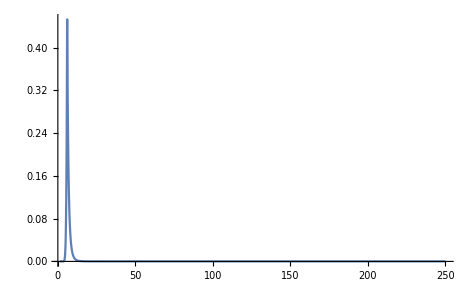

```mathematica
(* Try plotting modes. *)
ll=8;qi=2;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
(*Plot[Re[fn],{z,1.01,30.0},WorkingPrecision->30,PlotRange->All]*)
Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+SetPrecision[0.01,prec])/.mypar,SetPrecision[250,prec]},WorkingPrecision->prec,PlotRange->All]
```

```mathematica
(* Now export this to file and compare with numerical data from the 2+1D mode. *)
ll=7;
rmin=(rp/.mypar)+0.02;
rmax=35;dr=0.05;
rpts=Round[(rmax-rmin)/dr];
rvals=Table[rmin+dr*kk,{kk,0,rpts}];
rstarvals=Map[TortoiseCoord,rvals];
For[qi=1,qi<=5,qi++,
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
tmp=Table[ReIm[fn/.{z->Getznum[SetPrecision[rvals[[kk]],prec]]}],{kk,1,rpts+1}];
outdat[qi]=Transpose@tmp;
]
filen=NotebookDirectory[]<>"DataAnalysis/hprofile_fillvat_m0_a"<>ToString[StringForm["``",NumberForm[aval,2]]]<> "_l"<>ToString[ll]<>".dat";
(* One of these components (hlpmp) can have a real and imaginary part. *)
dset=Transpose@{rvals,rstarvals,outdat[1][[1]],outdat[2][[1]],outdat[3][[1]],outdat[3][[2]],outdat[4][[1]],outdat[5][[1]]};
Export[filen,dset]
```

/Users/sm1srd/Code/KerrLorenz/DataAnalysis/hprofile_fillvat_m0_a0.60_l7.dat

Show::gcomb: Could not combine the graphics objects in Show[figschw,].

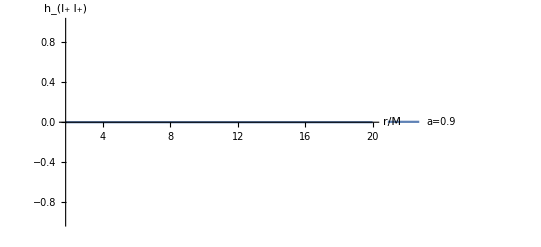
Show[figschw,-Graphics-]

/Users/sm1srd/Code/KerrLorenz/modefig.pdf

```mathematica
figkerr=Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.001)/.mypar,20.0},WorkingPrecision->30,PlotRange->All,AxesLabel->{r/M, ToExpression["h_{l_+ l_+}",TeXForm,HoldForm]},PlotLegends->{"a=0.9"}];
fig=Show[figschw,figkerr]
Export[mypath<>"modefig.pdf",fig]
```

#### Plot additional modes

Plot::precw: The precision of the argument function (Re[«1»]) is less than WorkingPrecision (30.).

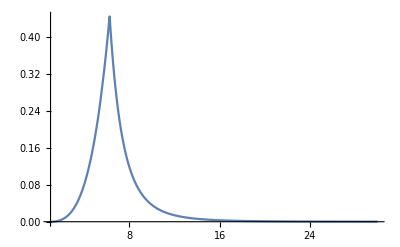

$Aborted

```mathematica
(* Try plotting modes *)
ll=4;qi=1;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
Plot[Re[fn],{z,1.01,30.0},WorkingPrecision->30,PlotRange->All]
Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.001)/.mypar,25.0},WorkingPrecision->30,PlotRange->All]
```

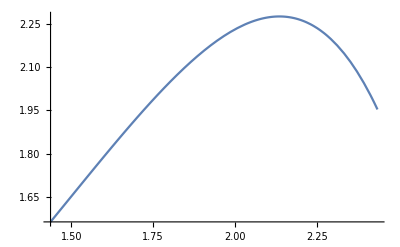

```mathematica
Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.0001)/.mypar,(rp+1.0)/.mypar},WorkingPrecision->30,PlotRange->All]
```

### Jumps in first derivatives

```mathematica
(* Check continuity and jumps in first derivatives *)
v0jump=GetEmptyVat[lmax];
v1jump=GetEmptyVat[lmax];
Monitor[
For[qi=1,qi<=5,qi++,
For[ll=0,ll<=lmax-4,ll++,
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,50];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,50];
v0jump[[qi,ll+1]]=(fout-fin)/.{z->z0}/.mypar;
v1jump[[qi,ll+1]]=(D[Getz[r],r]*D[fout-fin,z])/.{z->z0}/.mypar;
];
];,ll];
v0jump
```

{{-1.037591127037757957092185267727415120094872,0,11.784765677281311691741609162+0. ⅈ,0,-45.356019778350931756380640553+0. ⅈ,0,187.03396687744974136767045359+0. ⅈ,0,0,0,0},{0,0,378.003991972169336070086431653+0. ⅈ,0,-1244.9065722785001900192927834+0. ⅈ,0,4780.1286403949009816674887886+0. ⅈ,0,0,0,0},{0,0.+25.511386955716929303589752032 ⅈ,188.14152277926701429290402795+0. ⅈ,0.+55.843543792752632037963477174 ⅈ,-947.93208403747853601325896604+0. ⅈ,0.-175.30346792987701336253967865 ⅈ,4169.473544236445486173595056+0. ⅈ,0,0,0,0},{-135.40464708364898915666709825+0. ⅈ,0,-2155.9206008636455687255971781+0. ⅈ,0,13794.45042113165365402702614+0. ⅈ,0,-65176.7293636682276548100198+0. ⅈ,0,0,0,0},{0.386412896645494841827200530492056445648229,0,2.4007913580127969566816121081386711281518899,0,-7.288159966224586903861745615991030951317,0,27.0551646161317245046096434178518707,0,0,0,0}}

```mathematica
(* Look at the jumps in the first derivatives. We should be able to read these off from the projections of the stress-energy tensor that appear on the right-hand side of the wave equation. *)
ABCDsubs=GetABCD[mypar];
jumpampl[1]=-16*π/(ut*Δ)*A^2/.{r->r0}/.ABCDsubs/.mypar
jumpampl[2]=-16*π/(ut*Δ)*(-B^2)/.{r->r0}/.ABCDsubs/.mypar
jumpampl[3]=-16*π/(ut*Δ)*(-I*A*B*r0)/.{r->r0}/.ABCDsubs/.mypar
jumpampl[5]=-16*π/(ut*Δ)/.{r->r0}/.ABCDsubs/.mypar
(* Remember that it is hbar, not h, that satisfies the Lorenz-gauge equation. This only affects the 4th component, (Σ h_{mp mm}).*)
jumpampl[4]=r0^4*jumpampl[5]-16*π/(ut*Δ)*(B^2*r0^2)/.{r->r0}/.ABCDsubs/.mypar
```

-2.41974627591102811969605139615735735678158057575

5.80961350958675822848753578767203195821009096272

22.4962322079715923757832365279488424116210407515 ⅈ

-1.506230322104606928365874981972000112876136753381

-2161.22058379269387538772526499190529678303650704

```mathematica
-2161.220583792694/-209.1460863451232962255512883561931504955632746579615853689307`48.54423763307431
```

10.3335

```mathematica
(* Check that the jumps in the first derivatives are just as expected. *)
SpherHarms0=Table[SphericalHarmonicY[ll,0,π/2,0],{ll,0,lmax}]//N;
SpherHarms1=Table[SpinWeightedSphericalHarmonicY[-1,ll,0,π/2,0],{ll,0,lmax}]//N;
SpherHarms2=Table[SpinWeightedSphericalHarmonicY[-2,ll,0,π/2,0],{ll,0,lmax}]//N;
Table[Re[v1jump[[1]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Table[Re[v1jump[[2]][[ll+1]]/SpherHarms2[[ll+1]]],{ll,2,lmax-4,2}]
Table[Im[v1jump[[3]][[ll+1]]/SpherHarms1[[ll+1]]],{ll,1,lmax-4,2}]
Table[Re[v1jump[[4]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Table[Re[v1jump[[5]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Print["Differences :"]
Table[Re[v1jump[[1]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[1],{ll,0,lmax-4,2}]
Table[Re[v1jump[[2]][[ll+1]]/SpherHarms2[[ll+1]]]-jumpampl[2],{ll,2,lmax-4,2}]
Table[Im[v1jump[[3]][[ll+1]]/SpherHarms1[[ll+1]]]-Im[jumpampl[3]],{ll,1,lmax-4,2}]
Table[Re[v1jump[[4]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[4],{ll,0,lmax-4,2}]
Table[Re[v1jump[[5]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[5],{ll,0,lmax-4,2}]
(* All checks out. *)
```

{-2.41975,-2.41975,-2.41975,-2.41975}

{5.80961,5.80961,5.80961}

{22.4962,22.4962,22.4962}

{-2161.22,-2161.22,-2161.22,-2161.22}

{-1.50623,-1.50623,-1.50623,-1.50623}

Differences :

{0.,4.44089×10^-16,4.44089×10^-16,0.}

{-8.88178×10^-16,-8.88178×10^-16,0.}

{0.,0.,0.}

{0.,4.54747×10^-13,4.54747×10^-13,0.}

{0.,0.,2.22045×10^-16,-2.22045×10^-16}

## Numerical implementation (old version)

### Functions

```mathematica
CalculateLeftRightCoeffs[nsol1_,mypar_]:=Module[{Ainrepl,Aoutrepl,Ain0subs,Aout0subs},
(* Now we need to work out the coefficients from the jumps. *)
dzdr=D[Getz[r],r];
ABCDsubs=GetABCD[mypar];
For[ll=2,ll<=lmax+6,ll++,
Ainsubs[ll]={};
Aoutsubs[ll]={};
If[Mod[ll,2]==0,
(* spin 2 even *)
jumps= {J0e,J1e}/.Jumps2/.λsubs/.{l->ll}/.{S0->SpinWeightedSphericalHarmonicY[-2,ll,0,π/2,0]}/.ABCDsubs/.mypar;
fns=GetP2function[ll];
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout}]//First;
AppendTo[Ainsubs[ll],Aeven[ll]-> Ain/.Asol];
AppendTo[Aoutsubs[ll],Aeven[ll]-> Aout/.Asol];
(* trace *)
fns=Gethlfunction[ll];
jumps={0,J1h}/.λsubs/.{l->ll}/.{Y0->SphericalHarmonicY[ll,0,π/2,0]}/.ABCDsubs/.mypar;
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout}]//First;
AppendTo[Ainsubs[ll],(Atr[ll]->Ain)/.Asol];
AppendTo[Aoutsubs[ll],(Atr[ll]->Aout)/.Asol];
(* scalar *)
fns=Gethlfunction[ll];
jumps={Jsc0[ll],Jsc1[ll]}/.nsol1;
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout}]//First;
AppendTo[Ainsubs[ll],(Ascal[ll]->Ain)/.Asol];
AppendTo[Aoutsubs[ll],(Ascal[ll]->Aout)/.Asol];
,
(* spin 2 odd *)
jumps={J0o,J1o}/.Jumps2/.λsubs/.{l->ll}/.{S0p->D[SpinWeightedSphericalHarmonicY[-2,ll,0,θ,0],θ]/.{θ->π/2}}/.ABCDsubs/.mypar;
fns=GetP2function[ll];
eqs={Aout*fns[[2]]-Ain*fns[[1]]==jumps[[1]],dzdr*(Aout*D[fns[[2]],z]-Ain*D[fns[[1]],z])==jumps[[2]]}/.{z->z0}/.mypar;
Asol=Solve[eqs,{Ain,Aout}]//First;
AppendTo[Ainsubs[ll],Aodd[ll]-> Ain/.Asol];
AppendTo[Aoutsubs[ll],Aodd[ll]-> Aout/.Asol];
];
];
(* Now we need the jump conditions for the completion pieces *)
(* The following generates a solution with the right mass and angular momentum, but which is irregular at infinity due to the D solution,
and irregular at the horizon, due to the F solution. *)
(*
Ain0subs={coB->-(coB/.nsol1),coC->0,coD->0,coE->0,coAM->0,coF->-(coF/.nsol1)};(* minus signs because on the inside. *)
Aout0subs={coB->0,coC->(coC/.nsol1),coD->(coD/.nsol1),coE-> (coE/.Jumpmono/.ABCDsubs),coAM->(coAM/.Jumpmono/.ABCDsubs/.mypar),coF->0};
*)

(* Alternatively, add homogeneous modes to construct the Berndtson-plus solution, which is regular at the horizon and at infinity,
 and which is zero in the tr,tθ,rϕ,θϕ components. It has the wrong mass AND the wrong angular momentum. *)
(* It has zero in the D component in the exterior. *)
Ain0subs={coB->-(coB/.nsol1),coC->((-2*M*rp^2*coD-(a/6)*(rm^3+rm^2*rp+5*rm*rp^2-7*rp^3)*coF)/.nsol1),coD->(-coD/.nsol1),coE->(-M*coD/.nsol1),coAM->((-a*coD-rp*(rp-rm)^2/(rp+rm)*coF)/.nsol1),coF->-(coF/.nsol1)}/.mypar;(* minus signs in the expressions below because now on the inside. *)
Aout0subs={coB->0,coC->((coC-2*M*rp^2*coD-(a/6)*(rm^3+rm^2*rp+5*rm*rp^2-7*rp^3)*coF)/.nsol1),coD->0,coE-> ((coE-M*coD/.nsol1)/.Jumpmono/.ABCDsubs),coAM->((coAM-a*coD-rp*(rp-rm)^2/(rp+rm)*coF)/.nsol1/.Jumpmono/.ABCDsubs/.mypar),coF->0}/.mypar;

Ainrepl=Join[Ain0subs,Table[Ainsubs[ll],{ll,2,lmax}]//Flatten];
Aoutrepl=Join[Aout0subs,Table[Aoutsubs[ll],{ll,2,lmax}]//Flatten];
{Ainrepl,Aoutrepl,Ain0subs,Aout0subs}
];
```

```mathematica
GetAllRadialFunctions[{Ainrepl_,Aoutrepl_},mypar_]:=Module[{fnsin,fnsout},
fnsin={};
fnsout={};
For[ll=2,ll<=lmax,ll++,
If[Mod[ll,2]==0,
(* Trace functions *)
fnnames={"Z0","X0","DeltaB0"};
ampls={Atr[ll]/.Ainrepl,Atr[ll]/.Aoutrepl};
dzdr=D[Getz[r],r];
For[fnct=1,fnct<=Length[fnnames],fnct++,
fnname=fnnames[[fnct]];
fns=GetSmoothedFunction[fnname,ll,ampls,mypar];
AppendTo[fnsin,ToExpression[fnname][ll][r]->fns[[1]]];
AppendTo[fnsin,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[1]],z]/.mypar];
AppendTo[fnsout,ToExpression[fnname][ll][r]->fns[[2]]];
AppendTo[fnsout,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[2]],z]/.mypar];
];
AppendTo[fnsin,hl[ll][r]->Atr[ll]*Gethlfunction[ll][[1]]/.Ainrepl];
AppendTo[fnsin,hl[ll]'[r]->Atr[ll]*dzdr*D[Gethlfunction[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,hl[ll][r]->Atr[ll]*Gethlfunction[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,hl[ll]'[r]->Atr[ll]*dzdr*D[Gethlfunction[ll][[2]],z]/.Aoutrepl];
(* Even parity functions *)
fnnames={"χek0","χe"};
ampls={Aeven[ll]/.Ainrepl,Aeven[ll]/.Aoutrepl};
dzdr=D[Getz[r],r];
For[fnct=1,fnct<=Length[fnnames],fnct++,
fnname=fnnames[[fnct]];
fns=GetSmoothedFunction[fnname,ll,ampls,mypar];
AppendTo[fnsin,ToExpression[fnname][ll][r]->fns[[1]]];
AppendTo[fnsin,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[1]],z]/.mypar];
AppendTo[fnsout,ToExpression[fnname][ll][r]->fns[[2]]];
AppendTo[fnsout,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[2]],z]/.mypar];
];
AppendTo[fnsin,P2[ll][r]->Aeven[ll]*GetP2function[ll][[1]]/.Ainrepl];
AppendTo[fnsin,P2[ll]'[r]->Aeven[ll]*dzdr*D[GetP2function[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,P2[ll][r]->Aeven[ll]*GetP2function[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,P2[ll]'[r]->Aeven[ll]*dzdr*D[GetP2function[ll][[2]],z]/.Aoutrepl];
(* Free scalar functions *)
AppendTo[fnsin,R0[ll][r]->Ascal[ll]*Gethlfunction[ll][[1]]/.Ainrepl];
AppendTo[fnsin,R0[ll]'[r]->Ascal[ll]*dzdr*D[Gethlfunction[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,R0[ll][r]->Ascal[ll]*Gethlfunction[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,R0[ll]'[r]->Ascal[ll]*dzdr*D[Gethlfunction[ll][[2]],z]/.Aoutrepl];
,
(* Odd parity functions *)
fnnames={"χoc[-1]","χoc[1]","χos[-1]","χos[1]"};
ampls={Aodd[ll]/.Ainrepl,Aodd[ll]/.Aoutrepl};
dzdr=D[Getz[r],r];
For[fnct=1,fnct<=Length[fnnames],fnct++,
fnname=fnnames[[fnct]];
fns=GetSmoothedFunction[fnname,ll,ampls,mypar];
AppendTo[fnsin,ToExpression[fnname][ll][r]->fns[[1]]];
AppendTo[fnsin,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[1]],z]/.mypar];
AppendTo[fnsout,ToExpression[fnname][ll][r]->fns[[2]]];
AppendTo[fnsout,ToExpression[fnname][ll]'[r]->dzdr*D[fns[[2]],z]/.mypar];
];
AppendTo[fnsin,P2[ll][r]->Aodd[ll]*GetP2function[ll][[1]]/.Ainrepl];
AppendTo[fnsin,P2[ll]'[r]->Aodd[ll]*dzdr*D[GetP2function[ll][[1]],z]/.Ainrepl];
AppendTo[fnsout,P2[ll][r]->Aodd[ll]*GetP2function[ll][[2]]/.Aoutrepl];
AppendTo[fnsout,P2[ll]'[r]->Aodd[ll]*dzdr*D[GetP2function[ll][[2]],z]/.Aoutrepl];
];
];
{fnsin,fnsout}
];
```

### Schw

```mathematica
(* OK, choose our parameters and start a numerical calculation *)
mypar=SetParams[6.0`50,0.001`50]; (* At time of writing the process implemented above does not work for a exactly zero; but it seems to work fine for 'a' close to zero. Need to investigate. *)
VatJumpsNum=SetNumericalJumps[mypar];
{nsol1,checks1}=SolveJumpEquations[VatJumpsNum];
checks1 (* Excellent, the consistency equations are clearly satisfied. *)
```

50

{0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.}

```mathematica
TortoiseCoord[r_]:=
r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]-rm*Log[(r-rm)/2])/.mypar;
InvTortoise[x_?NumericQ]:=r/.FindRoot[TortoiseCoord[r]-x,{r,(rp+0.0000001)/.mypar}];
InvTortoise[TortoiseCoord[6]]
```

6.

```mathematica
{Ainrepl,Aoutrepl,Ain0subs,Aout0subs}=CalculateLeftRightCoeffs[nsol1,mypar];
{fnsin,fnsout}=GetAllRadialFunctions[{Ainrepl,Aoutrepl},mypar];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{2.49374821038799048862706×10^-10,-4.52846337448492166415796×10^14,0.000315539641605952868122436},{-5.58657238885185568156504×10^-10,-1.29760434461555546593592×10^15,-0.121562187158822870622662}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{5.69172991656642015751175×10^-14,-1.43457889275292444253257×10^11,0},{-1.51151844049729865935634×10^-13,-3.51083411944997301516865×10^11,0.471248777139694984674571}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{2.798554719570938391413×10^-11,-5.095371104781166126007×10^15,0.03027765576451169978579},{-6.840434738282538281414×10^-11,-1.564000523138346773007×10^16,0.01009461289642757507934}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

```mathematica
(* Note that the coefficients have been absorbed into the definition of the functions, as is required for the smoothing process. So now we set the coefficients to unity. *)
Getznum[rr_?NumericQ]=(2*rr-rp-rm)/(rp-rm)/.mypar;
Aunitysubs=Table[{Atr[ll]->1,Aeven[ll]->1,Aodd[ll]->1,Ascal[ll]->1},{ll,2,lmax+6}]//Flatten;
```

```mathematica
(* Check continuity *)
qi=5;ll=6;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,50];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,50];
fin/.{z->z0}/.mypar
fout/.{z->z0}/.mypar
```

-0.177421855643431972105555519012291361

-0.177421855643431972105555519012291361

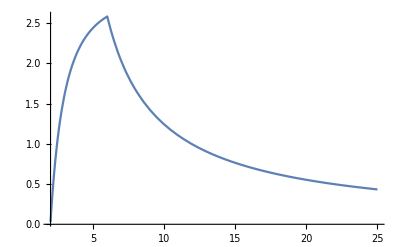

```mathematica
(* Try plotting modes. *)
ll=0;qi=1;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
(*Plot[Re[fn],{z,1.01,30.0},WorkingPrecision->30,PlotRange->All]*)
Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.01)/.mypar,25.0},WorkingPrecision->30,PlotRange->All]
```

```mathematica
(* Now export this to file and compare with numerical data from the 2+1D mode. *)
ll=3;
rmin=(rp/.mypar)+0.02;
rmax=30;dr=0.05;
rpts=Round[(rmax-rmin)/dr];
rvals=Table[rmin+dr*kk,{kk,0,rpts}];
rstarvals=Map[TortoiseCoord,rvals];
For[qi=1,qi<=5,qi++,
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
tmp=Table[ReIm[fn/.{z->Getznum[rvals[[kk]]]}],{kk,1,rpts+1}];
outdat[qi]=Transpose@tmp;
]
filen=NotebookDirectory[]<>"DataAnalysis/hprofile_fillvat_m0_a0_l"<>ToString[ll]<>".dat";
(* One of these components can have a real and imaginary part *)
dset=Transpose@{rvals,rstarvals,outdat[1][[1]],outdat[2][[1]],outdat[3][[1]],outdat[3][[2]],outdat[4][[1]],outdat[5][[1]]};
Export[filen,dset]
```

/Users/sm1srd/Code/KerrLorenz/DataAnalysis/hprofile_fillvat_m0_a0_l3.dat

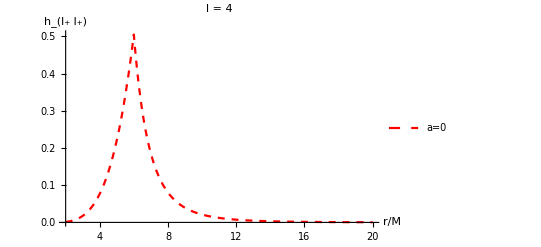

```mathematica
figschw=Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.001)/.mypar,20.0},WorkingPrecision->30,PlotRange->All,AxesLabel->{r/M, ToExpression["h_{l_+ l_+}",TeXForm,HoldForm]},PlotStyle->{{Dashed,Red}},PlotLegends->{"a=0"},PlotLabel->"l = 4"]
```

#### Jumps in first derivatives

```mathematica
(* Check continuity and jumps in first derivatives *)
v0jump=GetEmptyVat[lmax];
v1jump=GetEmptyVat[lmax];
Monitor[
For[qi=1,qi<=5,qi++,
For[ll=0,ll<=lmax-4,ll++,
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,50];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,50];
v0jump[[qi,ll+1]]=(fout-fin)/.{z->z0}/.mypar;
v1jump[[qi,ll+1]]=(D[Getz[r],r]*D[fout-fin,z])/.{z->z0}/.mypar;
];
];,ll];
v0jump
```

{{0.,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0,0,0},{0,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0,0,0},{0,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0,0,0,0},{0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0.+0. ⅈ,0,0,0,0},{0.,0,0.,0,0.,0,0.,0,0,0,0}}

```mathematica
(* Look at the jumps in the first derivatives. We should be able to read these off from the projections of the stress-energy tensor that appear on the right-hand side of the wave equation. *)
ABCDsubs=GetABCD[mypar];
jumpampl[1]=-16*π/(ut*Δ)*A^2/.{r->r0}/.ABCDsubs/.mypar
jumpampl[2]=-16*π/(ut*Δ)*(-B^2)/.{r->r0}/.ABCDsubs/.mypar
jumpampl[3]=-16*π/(ut*Δ)*(-I*A*B*r0)/.{r->r0}/.ABCDsubs/.mypar
jumpampl[5]=-16*π/(ut*Δ)/.{r->r0}/.ABCDsubs/.mypar
(* Remember that it is hbar, not h, that satisfies the Lorenz-gauge equation. This only affects the 4th component, (Σ h_{mp mm}).*)
jumpampl[4]=(-16*π/(ut*Δ)*(B^2*r0^2)/.{r->r0}/.ABCDsubs/.mypar)+(r0^4*jumpampl[5]/.mypar)
```

-2.96131735898230632683588148947456037939282576472

17.7533996822192910837127106573972964969952908812

43.5045310715636849887543307057289144038529427201 ⅈ

-1.481061663740928326184854775718712280083136301799

-2558.57830476813758974922937299775378887957511886

```mathematica
(* Check that the jumps in the first derivatives are just as expected. *)
SpherHarms0=Table[SphericalHarmonicY[ll,0,π/2,0],{ll,0,lmax}]//N;
SpherHarms1=Table[SpinWeightedSphericalHarmonicY[-1,ll,0,π/2,0],{ll,0,lmax}]//N;
SpherHarms2=Table[SpinWeightedSphericalHarmonicY[-2,ll,0,π/2,0],{ll,0,lmax}]//N;
Table[Re[v1jump[[1]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Table[Re[v1jump[[2]][[ll+1]]/SpherHarms2[[ll+1]]],{ll,2,lmax-4,2}]
Table[Im[v1jump[[3]][[ll+1]]/SpherHarms1[[ll+1]]],{ll,1,lmax-4,2}]
Table[Re[v1jump[[4]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Table[Re[v1jump[[5]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Print["Differences :"]
Table[Re[v1jump[[1]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[1],{ll,0,lmax-4,2}]
Table[Re[v1jump[[2]][[ll+1]]/SpherHarms2[[ll+1]]]-jumpampl[2],{ll,2,lmax-4,2}]
Table[Im[v1jump[[3]][[ll+1]]/SpherHarms1[[ll+1]]]-Im[jumpampl[3]],{ll,1,lmax-4,2}]
Table[Re[v1jump[[4]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[4],{ll,0,lmax-4,2}]
Table[Re[v1jump[[5]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[5],{ll,0,lmax-4,2}]
(* All checks out. *)
(* Good, this is working*)
```

{-2.96132,-2.96132,-2.96132,-2.96132}

{17.7534,17.7534,17.7534}

{43.5045,43.5045,43.5045}

{-2558.58,-2558.58,-2558.58,-2558.58}

{-1.48106,-1.48106,-1.48106,-1.48106}

Differences :

{0.,4.44089×10^-16,4.44089×10^-16,0.}

{-3.55271×10^-15,-3.55271×10^-15,-3.55271×10^-15}

{0.,-7.10543×10^-15,0.}

{0.,0.,0.,-4.54747×10^-13}

{0.,2.22045×10^-16,2.22045×10^-16,0.}

```mathematica
Table[Re[v1jump[[3]][[ll+1]]],{ll,2,lmax-4,2}] (* Note: even l here, odd l above. *)
(* This part does not have a jump in its derivative, as expected. *)
```

{0.,0.,0.}

### Kerr

```mathematica
(* OK, choose our parameters and start a numerical calculation *)
prec=50
aval=0.6`50;
r0val=6.0`50;
mypar=SetPrecision[SetParams[r0val,aval],prec]
VatJumpsNum=SetNumericalJumps[mypar];
{nsol1,checks1}=SolveJumpEquations[VatJumpsNum];
checks1 (* Excellent, the consistency equations are clearly satisfied. *)
{Ainrepl,Aoutrepl,Ain0subs,Aout0subs}=CalculateLeftRightCoeffs[nsol1,mypar];
{fnsin,fnsout}=GetAllRadialFunctions[{Ainrepl,Aoutrepl},mypar];
```

50

{M→1.,a→0.6,rp→1.8,rm→0.2,r0→6.,z0→6.25}

{0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.,0.,0.,0. ⅈ,0.,0.}

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.46665989086751321883665×10^-10,-4.89105963213599625039557×10^14,-0.0335689580386034367793005},{-2.9669552601448320180266×10^-10,-1.29067775116937702228701×10^15,-0.0130046915663188777416739}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.322455507809441228381×10^-11,-6.987026022395750689361×10^15,0.0001507836981598411511781},{-2.943104360857988280913×10^-11,-1.98527846789700423832×10^16,-0.1003125387577450641017}} may contain significant numerical errors.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{2.977097898579151868273×10^-15,-2.177847218187269131378×10^12,0},{-7.845265713587284565162×10^-15,-5.292043769584490857698×10^12,0.481086047561738264478}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

```mathematica
TortoiseCoord[r_]:=
r+(rp+rm)/(rp-rm)*(rp*Log[(r-rp)/2]-rm*Log[(r-rm)/2])/.mypar;
InvTortoise[x_?NumericQ]:=r/.FindRoot[TortoiseCoord[r]-x,{r,(rp+0.0000001)/.mypar}];
InvTortoise[TortoiseCoord[6]]
```

6.

```mathematica
(* Note that the coefficients have been absorbed into the definition of the functions, as is required for the smoothing process. So now we set the coefficients to unity. *)
Getznum[rr_?NumericQ]=(2*rr-rp-rm)/(rp-rm)/.mypar;
Aunitysubs=Table[{Atr[ll]->1,Aeven[ll]->1,Aodd[ll]->1,Ascal[ll]->1},{ll,2,lmax+6}]//Flatten;
```

```mathematica
(* Quickly check continuity *)
qi=5;ll=6;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,50];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,50];
fin/.{z->z0}/.mypar
fout/.{z->z0}/.mypar
```

-0.182470363134828219960355571963775

-0.182470363134828219960355571963775

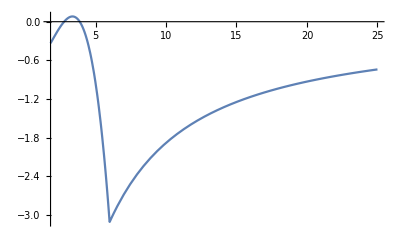

```mathematica
(* Try plotting modes. *)
ll=2;qi=2;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
(*Plot[Re[fn],{z,1.01,30.0},WorkingPrecision->30,PlotRange->All]*)
Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.01)/.mypar,25.0},WorkingPrecision->30,PlotRange->All]
```

```mathematica
(* Now export this to file and compare with numerical data from the 2+1D mode. *)
ll=7;
rmin=(rp/.mypar)+0.02;
rmax=35;dr=0.05;
rpts=Round[(rmax-rmin)/dr];
rvals=Table[rmin+dr*kk,{kk,0,rpts}];
rstarvals=Map[TortoiseCoord,rvals];
For[qi=1,qi<=5,qi++,
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->SetPrecision[Getr[z],prec]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
tmp=Table[ReIm[fn/.{z->Getznum[SetPrecision[rvals[[kk]],prec]]}],{kk,1,rpts+1}];
outdat[qi]=Transpose@tmp;
]
filen=NotebookDirectory[]<>"DataAnalysis/hprofile_fillvat_m0_a"<>ToString[StringForm["``",NumberForm[aval,2]]]<> "_l"<>ToString[ll]<>".dat";
(* One of these components (hlpmp) can have a real and imaginary part. *)
dset=Transpose@{rvals,rstarvals,outdat[1][[1]],outdat[2][[1]],outdat[3][[1]],outdat[3][[2]],outdat[4][[1]],outdat[5][[1]]};
Export[filen,dset]
```

/Users/sm1srd/Code/KerrLorenz/DataAnalysis/hprofile_fillvat_m0_a0.60_l7.dat

```mathematica
figkerr=Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.001)/.mypar,20.0},WorkingPrecision->30,PlotRange->All,AxesLabel->{r/M, ToExpression["h_{l_+ l_+}",TeXForm,HoldForm]},PlotLegends->{"a=0.9"}];
fig=Show[figschw,figkerr]
Export[mypath<>"modefig.pdf",fig]
```

Show::gcomb: Could not combine the graphics objects in Show[figschw,].

Show[figschw,-Graphics-]

/Users/sm1srd/Code/KerrLorenz/modefig.pdf

#### Plot additional modes

```mathematica
(* Try plotting modes *)
ll=4;qi=1;
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,prec];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,prec];
fn=N[(fin*HeavisideTheta[z0-z]+fout*HeavisideTheta[z-z0])/.mypar,prec];
Plot[Re[fn],{z,1.01,30.0},WorkingPrecision->30,PlotRange->All]
Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.001)/.mypar,25.0},WorkingPrecision->30,PlotRange->All]
```

Plot::precw: The precision of the argument function (Re[«1»]) is less than WorkingPrecision (30.).

-Graphics-

$Aborted

```mathematica
Plot[Re[fn/.{z->Getznum[rr]}],{rr,(rp+0.0001)/.mypar,(rp+1.0)/.mypar},WorkingPrecision->30,PlotRange->All]
```

-Graphics-

### Jumps in first derivatives

```mathematica
(* Check continuity and jumps in first derivatives *)
v0jump=GetEmptyVat[lmax];
v1jump=GetEmptyVat[lmax];
Monitor[
For[qi=1,qi<=5,qi++,
For[ll=0,ll<=lmax-4,ll++,
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Ain0subs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,50];
fout=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Aout0subs/.Aunitysubs/.fnsout/.{r->Getr[z]}/.mypar,50];
v0jump[[qi,ll+1]]=(fout-fin)/.{z->z0}/.mypar;
v1jump[[qi,ll+1]]=(D[Getz[r],r]*D[fout-fin,z])/.{z->z0}/.mypar;
];
];,ll];
v0jump
```

{{-1.037591127037757957092185267727415120094872,0,11.784765677281311691741609162+0. ⅈ,0,-45.356019778350931756380640553+0. ⅈ,0,187.03396687744974136767045359+0. ⅈ,0,0,0,0},{0,0,378.003991972169336070086431653+0. ⅈ,0,-1244.9065722785001900192927834+0. ⅈ,0,4780.1286403949009816674887886+0. ⅈ,0,0,0,0},{0,0.+25.511386955716929303589752032 ⅈ,188.14152277926701429290402795+0. ⅈ,0.+55.843543792752632037963477174 ⅈ,-947.93208403747853601325896604+0. ⅈ,0.-175.30346792987701336253967865 ⅈ,4169.473544236445486173595056+0. ⅈ,0,0,0,0},{-135.40464708364898915666709825+0. ⅈ,0,-2155.9206008636455687255971781+0. ⅈ,0,13794.45042113165365402702614+0. ⅈ,0,-65176.7293636682276548100198+0. ⅈ,0,0,0,0},{0.386412896645494841827200530492056445648229,0,2.4007913580127969566816121081386711281518899,0,-7.288159966224586903861745615991030951317,0,27.0551646161317245046096434178518707,0,0,0,0}}

```mathematica
(* Look at the jumps in the first derivatives. We should be able to read these off from the projections of the stress-energy tensor that appear on the right-hand side of the wave equation. *)
ABCDsubs=GetABCD[mypar];
jumpampl[1]=-16*π/(ut*Δ)*A^2/.{r->r0}/.ABCDsubs/.mypar
jumpampl[2]=-16*π/(ut*Δ)*(-B^2)/.{r->r0}/.ABCDsubs/.mypar
jumpampl[3]=-16*π/(ut*Δ)*(-I*A*B*r0)/.{r->r0}/.ABCDsubs/.mypar
jumpampl[5]=-16*π/(ut*Δ)/.{r->r0}/.ABCDsubs/.mypar
(* Remember that it is hbar, not h, that satisfies the Lorenz-gauge equation. This only affects the 4th component, (Σ h_{mp mm}).*)
jumpampl[4]=r0^4*jumpampl[5]-16*π/(ut*Δ)*(B^2*r0^2)/.{r->r0}/.ABCDsubs/.mypar
```

-2.41974627591102811969605139615735735678158057575

5.80961350958675822848753578767203195821009096272

22.4962322079715923757832365279488424116210407515 ⅈ

-1.506230322104606928365874981972000112876136753381

-2161.22058379269387538772526499190529678303650704

```mathematica
-2161.220583792694/-209.1460863451232962255512883561931504955632746579615853689307`48.54423763307431
```

10.3335

```mathematica
(* Check that the jumps in the first derivatives are just as expected. *)
SpherHarms0=Table[SphericalHarmonicY[ll,0,π/2,0],{ll,0,lmax}]//N;
SpherHarms1=Table[SpinWeightedSphericalHarmonicY[-1,ll,0,π/2,0],{ll,0,lmax}]//N;
SpherHarms2=Table[SpinWeightedSphericalHarmonicY[-2,ll,0,π/2,0],{ll,0,lmax}]//N;
Table[Re[v1jump[[1]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Table[Re[v1jump[[2]][[ll+1]]/SpherHarms2[[ll+1]]],{ll,2,lmax-4,2}]
Table[Im[v1jump[[3]][[ll+1]]/SpherHarms1[[ll+1]]],{ll,1,lmax-4,2}]
Table[Re[v1jump[[4]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Table[Re[v1jump[[5]][[ll+1]]/SpherHarms0[[ll+1]]],{ll,0,lmax-4,2}]
Print["Differences :"]
Table[Re[v1jump[[1]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[1],{ll,0,lmax-4,2}]
Table[Re[v1jump[[2]][[ll+1]]/SpherHarms2[[ll+1]]]-jumpampl[2],{ll,2,lmax-4,2}]
Table[Im[v1jump[[3]][[ll+1]]/SpherHarms1[[ll+1]]]-Im[jumpampl[3]],{ll,1,lmax-4,2}]
Table[Re[v1jump[[4]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[4],{ll,0,lmax-4,2}]
Table[Re[v1jump[[5]][[ll+1]]/SpherHarms0[[ll+1]]]-jumpampl[5],{ll,0,lmax-4,2}]
(* All checks out. *)
```

{-2.41975,-2.41975,-2.41975,-2.41975}

{5.80961,5.80961,5.80961}

{22.4962,22.4962,22.4962}

{-2161.22,-2161.22,-2161.22,-2161.22}

{-1.50623,-1.50623,-1.50623,-1.50623}

Differences :

{0.,4.44089×10^-16,4.44089×10^-16,0.}

{-8.88178×10^-16,-8.88178×10^-16,0.}

{0.,0.,0.}

{0.,4.54747×10^-13,4.54747×10^-13,0.}

{0.,0.,2.22045×10^-16,-2.22045×10^-16}

## Testing (old version)

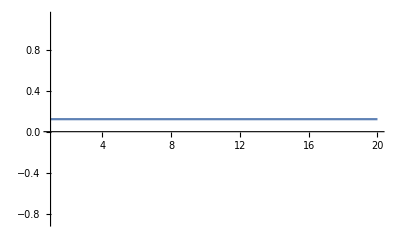

```mathematica
(* Try switching some things off. *)
qi=1; ll=2;
Azerosubs=Table[{Atr[ll]->0,Aeven[ll]->0,Aodd[ll]->0},{ll,2,lmax+6}]//Flatten;
A0zerosubs={coB->0,coC->0,coD->0,coE->0,coF->0,coAM->0};
fin=N[Vat[[qi]][[ll+1]]/.reverselogrepl/.Azerosubs/.A0zerosubs/.Aunitysubs/.fnsin/.{r->Getr[z]}/.mypar,50];
Plot[Re[fin],{z,1.001,20.0},WorkingPrecision->30,PlotRange->All]
```

```mathematica
v=GetEmptyVat[6];
v=AddVat[coB*hcompB,v];
v=AddVat[coC*hcompC,v];
v=AddVat[coD*hcompD,v];
v=AddVat[coE*hcompE,v];
v=AddVat[coF*hcompF,v];
v=AddVat[coAM*hcompAM,v];
 v=(v+Asc*PourFreeScalar[6,2,1])/.cosubs;
```

```mathematica
R0repl={R0[2]''[r]->D[D[LegendreQ[2,0,3,Getz[r]],r],r],R0[2]'[r]->D[LegendreQ[2,0,3,Getz[r]],r],R0[2][r]->LegendreQ[2,0,3,Getz[r]]};
```

```mathematica
t0=v[[1,1]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Series[t0,{r,rp,0}];
eq1A=Simplify[SeriesCoefficient[t1,-2],Assumptions->assum2]
eq2B=Simplify[SeriesCoefficient[t1,-1],Assumptions->assum2]
t2=Simplify[SeriesCoefficient[t1,0],Assumptions->assum2]
logeq1=Simplify[Coefficient[t2,Log[r-rp]],Assumptions->assum2]
```

1/(3 (rm-rp)^2)2 √π (6 coC (rm-rp)+4 coE rm^2 rp-coD rm^3 rp+6 coE rm rp^2-3 coD rm^2 rp^2+6 coE rp^3+coD rm rp^3+3 coD rp^4-8 coAM (rm rp)^(3/2)+coF rm^2 (rm rp)^(3/2)-coF rp^2 (rm rp)^(3/2)+coF (rm rp)^(5/2)-coAM √(rm^5 rp)-coF √(rm^9 rp)-7 coAM √(rm rp^5)-2 (rm-rp) (rm+rp)^2 (-2 coE+coD (rm+rp)) Log[-rm+rp])

1/(3 (rm-rp)^3)16 √π (4 coE rm rp^2-2 coAM (rm rp)^(3/2)+coF rm^2 (rm rp)^(3/2)-coF rp^2 (rm rp)^(3/2)-coF (rm rp)^(5/2)-coAM √(rm^5 rp)-coAM √(rm rp^5)+coF √(rm rp^9)+coD rm rp (rm^2-rp^2))

1/(3 (rm-rp)^4)2 √π (-6 coC rm+6 coC rp+32 coE rm^2 rp-24 coB rm^3 rp+23 coD rm^3 rp+10 coE rm rp^2+48 coB rm^2 rp^2-39 coD rm^2 rp^2+6 coE rp^3-24 coB rm rp^3+25 coD rm rp^3-9 coD rp^4-24 coAM (rm rp)^(3/2)+23 coF rm^2 (rm rp)^(3/2)+41 coF rp^2 (rm rp)^(3/2)-57 coF (rm rp)^(5/2)-15 coAM √(rm^5 rp)+coF √(rm^9 rp)-9 coAM √(rm rp^5)-8 coF √(rm rp^9)+8 rm (rm-rp) rp (-2 coE+coD (rm+rp)) Log[r-rp]+2 (rm-rp)^3 (-2 coE+coD (rm+rp)) Log[-rm+rp])

(16 √π rm rp (-2 coE+coD (rm+rp)))/(3 (rm-rp)^3)

```mathematica
t0=v[[4,1]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2];
t2=Simplify[Simplify[SeriesCoefficient[t1,0],Assumptions->assum2]/.Log[(2 (r-rp))/(-rm+rp)]->Log[2]+Log[r-rp]-Log[rp-rm],Assumptions->assum2]
logeq2=Simplify[Coefficient[t2,Log[r-rp]],Assumptions->assum2]
(* trysubs=Solve[{t2a==0,t2b==0},{coC,coAM}]//First *)
```

1/(15 (rm-rp)^3)4 rp (30 coC √π rm^3+18 √5 Asc rm^4-90 coC √π rm^2 rp-54 √5 Asc rm^3 rp+4 coE √π rm^4 rp+8 coB √π rm^5 rp+coD √π rm^5 rp+10 coAM √π rm^(7/2) rp^(3/2)+13 coF √π rm^(11/2) rp^(3/2)+90 coC √π rm rp^2+54 √5 Asc rm^2 rp^2-94 coE √π rm^3 rp^2-24 coB √π rm^4 rp^2+31 coD √π rm^4 rp^2-12 coF √π rm^(9/2) rp^(5/2)-30 coC √π rp^3-18 √5 Asc rm rp^3-46 coE √π rm^2 rp^3+24 coB √π rm^3 rp^3+94 coD √π rm^3 rp^3-10 coAM √π rm^(3/2) rp^(7/2)+70 coE √π rm rp^4-8 coB √π rm^2 rp^4-30 coD √π rm^2 rp^4-37 coF √π rm^(5/2) rp^(9/2)-30 coE √π rp^5-15 coD √π rm rp^5+33 coF √π rm^(3/2) rp^(11/2)+15 coD √π rp^6+18 coF √π (rm rp)^(7/2)-5 coAM √π √(rm^9 rp)-5 coF √π √(rm^13 rp)+5 coAM √π √(rm rp^9)-10 coF √π √(rm rp^13)+2 (3 √5 Asc rm (rm-rp)^3+8 √π rm^3 rp^2 (-2 coE+coD (rm+rp))) Log[r-rp]-2 (3 √5 Asc rm (rm-rp)^3+√π (5 rm^5-5 rm^4 rp-2 rm^3 rp^2+10 rm^2 rp^3+5 rm rp^4-5 rp^5) (-2 coE+coD (rm+rp))) Log[-rm+rp])

(8 Asc rm rp)/(√5)+(64 √π rm^3 rp^3 (-2 coE+coD (rm+rp)))/(15 (rm-rp)^3)

```mathematica
t0=v[[3,2]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2];
t2=SeriesCoefficient[t1,-1];
eq3B=Simplify[t2,Assumptions->assum2];
t2=Simplify[SeriesCoefficient[t1,0],Assumptions->assum2]
logeq3=Simplify[Coefficient[t2,Log[r-rp]],Assumptions->assum2]
```

-1/(15 (rm-rp)^7)2 ⅈ √(2/3) (30 coAM √π rm^7 rp+5 coF √π rm^9 rp+150 coC √π rm^(9/2) rp^(3/2)+396 √5 Asc rm^(11/2) rp^(3/2)+64 coE √π rm^(13/2) rp^(3/2)-30 coB √π rm^(15/2) rp^(3/2)-32 coD √π rm^(15/2) rp^(3/2)-135 coAM √π rm^6 rp^2-17 coF √π rm^8 rp^2-300 coC √π rm^(7/2) rp^(5/2)-990 √5 Asc rm^(9/2) rp^(5/2)+62 coE √π rm^(11/2) rp^(5/2)+90 coB √π rm^(13/2) rp^(5/2)+12 coD √π rm^(13/2) rp^(5/2)+210 coAM √π rm^5 rp^3+41 coF √π rm^7 rp^3+300 coC √π rm^(5/2) rp^(7/2)-566 coE √π rm^(9/2) rp^(7/2)+90 coB √π rm^(11/2) rp^(7/2)-168 coD √π rm^(11/2) rp^(7/2)-75 coAM √π rm^4 rp^4-229 coF √π rm^6 rp^4-150 coC √π rm^(3/2) rp^(9/2)-990 √5 Asc rm^(5/2) rp^(9/2)+716 coE √π rm^(7/2) rp^(9/2)-150 coAM √π rm^3 rp^5+835 coF √π rm^5 rp^5+396 √5 Asc rm^(3/2) rp^(11/2)-332 coE √π rm^(5/2) rp^(11/2)+1350 coB √π rm^(7/2) rp^(11/2)-1392 coD √π rm^(7/2) rp^(11/2)+195 coAM √π rm^2 rp^6-1615 coF √π rm^4 rp^6+86 coE √π rm^(3/2) rp^(13/2)-1170 coB √π rm^(5/2) rp^(13/2)+948 coD √π rm^(5/2) rp^(13/2)-90 coAM √π rm rp^7+1787 coF √π rm^3 rp^7+510 coB √π rm^(3/2) rp^(15/2)-328 coD √π rm^(3/2) rp^(15/2)+15 coAM √π rp^8-1151 coF √π rm^2 rp^8+404 coF √π rm rp^9-60 coF √π rp^10+1320 √5 Asc (rm rp)^(7/2)-750 coB √π (rm rp)^(9/2)+900 coD √π (rm rp)^(9/2)-30 coC √π √(rm^11 rp)-66 √5 Asc √(rm^13 rp)+30 coC √π √(rm rp^11)-66 √5 Asc √(rm rp^13)-30 coE √π √(rm rp^15)-90 coB √π √(rm rp^17)+60 coD √π √(rm rp^17)-6 (6 √5 Asc (-6 rm^(11/2) rp^(3/2)+15 rm^(9/2) rp^(5/2)+15 rm^(5/2) rp^(9/2)-6 rm^(3/2) rp^(11/2)-20 (rm rp)^(7/2)+√(rm^13 rp)+√(rm rp^13))+√π (-2 coE (rm^(13/2) rp^(3/2)+6 rm^(11/2) rp^(5/2)-13 rm^(9/2) rp^(7/2)-12 rm^(7/2) rp^(9/2)+39 rm^(5/2) rp^(11/2)-26 rm^(3/2) rp^(13/2)+5 √(rm rp^15))+coD (rm^(15/2) rp^(3/2)+7 rm^(13/2) rp^(5/2)-7 rm^(11/2) rp^(7/2)+27 rm^(7/2) rp^(11/2)+13 rm^(5/2) rp^(13/2)-21 rm^(3/2) rp^(15/2)-25 (rm rp)^(9/2)+5 √(rm rp^17)))) Log[r-rp]+2 (18 √5 Asc (-6 rm^(11/2) rp^(3/2)+15 rm^(9/2) rp^(5/2)+15 rm^(5/2) rp^(9/2)-6 rm^(3/2) rp^(11/2)-20 (rm rp)^(7/2)+√(rm^13 rp)+√(rm rp^13))+√π (-2 coE (-12 rm^(13/2) rp^(3/2)+23 rm^(11/2) rp^(5/2)-14 rm^(9/2) rp^(7/2)-61 rm^(7/2) rp^(9/2)+112 rm^(5/2) rp^(11/2)-63 rm^(3/2) rp^(13/2)+5 √(rm^15 rp)+10 √(rm rp^15))+coD (-7 rm^(15/2) rp^(3/2)+11 rm^(13/2) rp^(5/2)+9 rm^(11/2) rp^(7/2)+51 rm^(7/2) rp^(11/2)+49 rm^(5/2) rp^(13/2)-53 rm^(3/2) rp^(15/2)-75 (rm rp)^(9/2)+5 √(rm^17 rp)+10 √(rm rp^17)))) Log[-rm+rp])

1/(5 (rm-rp)^7)4 ⅈ √(2/3) (6 √5 Asc (-6 rm^(11/2) rp^(3/2)+15 rm^(9/2) rp^(5/2)+15 rm^(5/2) rp^(9/2)-6 rm^(3/2) rp^(11/2)-20 (rm rp)^(7/2)+√(rm^13 rp)+√(rm rp^13))+√π (-2 coE (rm^(13/2) rp^(3/2)+6 rm^(11/2) rp^(5/2)-13 rm^(9/2) rp^(7/2)-12 rm^(7/2) rp^(9/2)+39 rm^(5/2) rp^(11/2)-26 rm^(3/2) rp^(13/2)+5 √(rm rp^15))+coD (rm^(15/2) rp^(3/2)+7 rm^(13/2) rp^(5/2)-7 rm^(11/2) rp^(7/2)+27 rm^(7/2) rp^(11/2)+13 rm^(5/2) rp^(13/2)-21 rm^(3/2) rp^(15/2)-25 (rm rp)^(9/2)+5 √(rm rp^17))))

```mathematica
t0=v[[1,3]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2];
eq4A=Simplify[SeriesCoefficient[t1,-2],Assumptions->assum2]
eq5B=Simplify[SeriesCoefficient[t1,-1],Assumptions->assum2]
t2=Simplify[SeriesCoefficient[t1,0],Assumptions->assum2]
logeq4=Simplify[Coefficient[t2,Log[r-rp]],Assumptions->assum2]
```

Asc+1/(3 (rm-rp)^3)4 √(π/5) (coF rm^(9/2) rp^(3/2)-2 coF rm^(7/2) rp^(5/2)-4 coE rm rp^3+2 coF rm^(3/2) rp^(9/2)-coF √(rm rp^11)+coD rm rp (rm^3+rm^2 rp+rm rp^2+rp^3)+coAM (-rm^(5/2) rp^(3/2)+rm^(3/2) rp^(5/2)-√(rm^7 rp)+√(rm rp^7)))

(6 Asc)/(rm-rp)+1/(3 (rm-rp)^4)8 √(π/5) (coF rm^(9/2) rp^(3/2)-8 coE rm^2 rp^2-2 coF rm^(7/2) rp^(5/2)-4 coE rm rp^3+2 coF rm^(3/2) rp^(9/2)-coF √(rm rp^11)+coD rm rp (rm^3+5 rm^2 rp+5 rm rp^2+rp^3)+coAM (-rm^(5/2) rp^(3/2)+rm^(3/2) rp^(5/2)-√(rm^7 rp)+√(rm rp^7)))

-1/(15 (rm-rp)^5)(105 Asc rm^3-315 Asc rm^2 rp-48 coE √(5 π) rm^3 rp+12 coD √(5 π) rm^4 rp+12 coAM √(5 π) rm^(5/2) rp^(3/2)-44 coF √(5 π) rm^(9/2) rp^(3/2)+315 Asc rm rp^2-64 coE √(5 π) rm^2 rp^2+44 coD √(5 π) rm^3 rp^2-12 coAM √(5 π) rm^(3/2) rp^(5/2)+120 coF √(5 π) rm^(7/2) rp^(5/2)-105 Asc rp^3+44 coD √(5 π) rm^2 rp^3-96 coF √(5 π) rm^(5/2) rp^(7/2)+12 coD √(5 π) rm rp^4+8 coF √(5 π) rm^(3/2) rp^(9/2)+12 coAM √(5 π) √(rm^7 rp)-12 coAM √(5 π) √(rm rp^7)+12 coF √(5 π) √(rm rp^11)+4 (45 Asc (rm-rp)^3+4 √(5 π) rm rp (rm^2+4 rm rp+rp^2) (-2 coE+coD (rm+rp))) Log[r-rp]-4 (45 Asc (rm-rp)^3+4 √(5 π) rm rp (rm^2+4 rm rp+rp^2) (-2 coE+coD (rm+rp))) Log[-rm+rp])

-(4 (45 Asc (rm-rp)^3+4 √(5 π) rm rp (rm^2+4 rm rp+rp^2) (-2 coE+coD (rm+rp))))/(15 (rm-rp)^5)

```mathematica
t0=v[[2,3]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2]
t2=SeriesCoefficient[t1,0]
logeq5=Simplify[Coefficient[t2,Log[r-rp]],Assumptions->assum2]
```

1/(5 (rm-rp)^3)2 √(2/3) (-45 Asc rm^3+135 Asc rm^2 rp+8 coE √(5 π) rm^3 rp-4 coB √(5 π) rm^4 rp+4 coF √(5 π) rm^(9/2) rp^(3/2)-135 Asc rm rp^2+32 coE √(5 π) rm^2 rp^2+12 coB √(5 π) rm^3 rp^2-32 coD √(5 π) rm^3 rp^2-16 coF √(5 π) rm^(7/2) rp^(5/2)+45 Asc rp^3+8 coE √(5 π) rm rp^3-12 coB √(5 π) rm^2 rp^3-8 coD √(5 π) rm^2 rp^3+24 coF √(5 π) rm^(5/2) rp^(7/2)+4 coB √(5 π) rm rp^4-8 coD √(5 π) rm rp^4-16 coF √(5 π) rm^(3/2) rp^(9/2)+4 coF √(5 π) √(rm rp^11)-15 Asc rm^3 Log[r-rp]+45 Asc rm^2 rp Log[r-rp]-45 Asc rm rp^2 Log[r-rp]+16 coE √(5 π) rm^2 rp^2 Log[r-rp]-8 coD √(5 π) rm^3 rp^2 Log[r-rp]+15 Asc rp^3 Log[r-rp]-8 coD √(5 π) rm^2 rp^3 Log[r-rp]+15 Asc rm^3 Log[-rm+rp]-45 Asc rm^2 rp Log[-rm+rp]+45 Asc rm rp^2 Log[-rm+rp]-16 coE √(5 π) rm^2 rp^2 Log[-rm+rp]+8 coD √(5 π) rm^3 rp^2 Log[-rm+rp]-15 Asc rp^3 Log[-rm+rp]+8 coD √(5 π) rm^2 rp^3 Log[-rm+rp])+O[r-rp]^1

1/(5 (rm-rp)^3)2 √(2/3) (-45 Asc rm^3+135 Asc rm^2 rp+8 coE √(5 π) rm^3 rp-4 coB √(5 π) rm^4 rp+4 coF √(5 π) rm^(9/2) rp^(3/2)-135 Asc rm rp^2+32 coE √(5 π) rm^2 rp^2+12 coB √(5 π) rm^3 rp^2-32 coD √(5 π) rm^3 rp^2-16 coF √(5 π) rm^(7/2) rp^(5/2)+45 Asc rp^3+8 coE √(5 π) rm rp^3-12 coB √(5 π) rm^2 rp^3-8 coD √(5 π) rm^2 rp^3+24 coF √(5 π) rm^(5/2) rp^(7/2)+4 coB √(5 π) rm rp^4-8 coD √(5 π) rm rp^4-16 coF √(5 π) rm^(3/2) rp^(9/2)+4 coF √(5 π) √(rm rp^11)-15 Asc rm^3 Log[r-rp]+45 Asc rm^2 rp Log[r-rp]-45 Asc rm rp^2 Log[r-rp]+16 coE √(5 π) rm^2 rp^2 Log[r-rp]-8 coD √(5 π) rm^3 rp^2 Log[r-rp]+15 Asc rp^3 Log[r-rp]-8 coD √(5 π) rm^2 rp^3 Log[r-rp]+15 Asc rm^3 Log[-rm+rp]-45 Asc rm^2 rp Log[-rm+rp]+45 Asc rm rp^2 Log[-rm+rp]-16 coE √(5 π) rm^2 rp^2 Log[-rm+rp]+8 coD √(5 π) rm^3 rp^2 Log[-rm+rp]-15 Asc rp^3 Log[-rm+rp]+8 coD √(5 π) rm^2 rp^3 Log[-rm+rp])

-2 √6 Asc-(16 √((2 π)/15) rm^2 rp^2 (-2 coE+coD (rm+rp)))/(rm-rp)^3

```mathematica
t0=v[[3,3]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2]
eq6B=Simplify[SeriesCoefficient[t1,-1],Assumptions->assum2]
t2=Simplify[SeriesCoefficient[t1,0],Assumptions->assum2]
logeq6=Simplify[Coefficient[t2,Log[r-rp]],Assumptions->assum2]
```

(-15 √6 Asc rm^3 rp+45 √6 Asc rm^2 rp^2-45 √6 Asc rm rp^3+16 coE √(30 π) rm^2 rp^3-8 coD √(30 π) rm^3 rp^3+15 √6 Asc rp^4-8 coD √(30 π) rm^2 rp^4)/(15 (rm-rp)^3 (r-rp))-1/(35 (rm-rp)^4)√(2/3) (-210 Asc rm^4-315 Asc rm^3 rp+56 coE √(5 π) rm^4 rp-28 coB √(5 π) rm^5 rp+34 coF √(5 π) rm^(11/2) rp^(3/2)+2205 Asc rm^2 rp^2+280 coE √(5 π) rm^3 rp^2+112 coB √(5 π) rm^4 rp^2-280 coD √(5 π) rm^4 rp^2-94 coF √(5 π) rm^(9/2) rp^(5/2)-2625 Asc rm rp^3+728 coE √(5 π) rm^2 rp^3-168 coB √(5 π) rm^3 rp^3-336 coD √(5 π) rm^3 rp^3+945 Asc rp^4+168 coE √(5 π) rm rp^4+112 coB √(5 π) rm^2 rp^4-560 coD √(5 π) rm^2 rp^4-220 coF √(5 π) rm^(5/2) rp^(9/2)-28 coB √(5 π) rm rp^5-56 coD √(5 π) rm rp^5+202 coF √(5 π) rm^(3/2) rp^(11/2)+148 coF √(5 π) (rm rp)^(7/2)-70 coF √(5 π) √(rm rp^13)-105 Asc rm^4 Log[r-rp]-210 Asc rm^3 rp Log[r-rp]+1260 Asc rm^2 rp^2 Log[r-rp]+224 coE √(5 π) rm^3 rp^2 Log[r-rp]-112 coD √(5 π) rm^4 rp^2 Log[r-rp]-1470 Asc rm rp^3 Log[r-rp]+336 coE √(5 π) rm^2 rp^3 Log[r-rp]-280 coD √(5 π) rm^3 rp^3 Log[r-rp]+525 Asc rp^4 Log[r-rp]+112 coE √(5 π) rm rp^4 Log[r-rp]-224 coD √(5 π) rm^2 rp^4 Log[r-rp]-56 coD √(5 π) rm rp^5 Log[r-rp]+105 Asc rm^4 Log[-rm+rp]+210 Asc rm^3 rp Log[-rm+rp]-1260 Asc rm^2 rp^2 Log[-rm+rp]-224 coE √(5 π) rm^3 rp^2 Log[-rm+rp]+112 coD √(5 π) rm^4 rp^2 Log[-rm+rp]+1470 Asc rm rp^3 Log[-rm+rp]-336 coE √(5 π) rm^2 rp^3 Log[-rm+rp]+280 coD √(5 π) rm^3 rp^3 Log[-rm+rp]-525 Asc rp^4 Log[-rm+rp]-112 coE √(5 π) rm rp^4 Log[-rm+rp]+224 coD √(5 π) rm^2 rp^4 Log[-rm+rp]+56 coD √(5 π) rm rp^5 Log[-rm+rp])+O[r-rp]^1

-√6 Asc rp-(8 √((2 π)/15) rm^2 rp^3 (-2 coE+coD (rm+rp)))/(rm-rp)^3

1/(35 (rm-rp)^4)√(2/3) (210 Asc rm^4+315 Asc rm^3 rp-56 coE √(5 π) rm^4 rp+28 coB √(5 π) rm^5 rp-34 coF √(5 π) rm^(11/2) rp^(3/2)-2205 Asc rm^2 rp^2-280 coE √(5 π) rm^3 rp^2-112 coB √(5 π) rm^4 rp^2+280 coD √(5 π) rm^4 rp^2+94 coF √(5 π) rm^(9/2) rp^(5/2)+2625 Asc rm rp^3-728 coE √(5 π) rm^2 rp^3+168 coB √(5 π) rm^3 rp^3+336 coD √(5 π) rm^3 rp^3-945 Asc rp^4-168 coE √(5 π) rm rp^4-112 coB √(5 π) rm^2 rp^4+560 coD √(5 π) rm^2 rp^4+220 coF √(5 π) rm^(5/2) rp^(9/2)+28 coB √(5 π) rm rp^5+56 coD √(5 π) rm rp^5-202 coF √(5 π) rm^(3/2) rp^(11/2)-148 coF √(5 π) (rm rp)^(7/2)+70 coF √(5 π) √(rm rp^13)+7 (15 Asc (rm-rp)^3 (rm+5 rp)+8 √(5 π) rm rp^2 (2 rm^2+3 rm rp+rp^2) (-2 coE+coD (rm+rp))) Log[r-rp]-7 (15 Asc (rm-rp)^3 (rm+5 rp)+8 √(5 π) rm rp^2 (2 rm^2+3 rm rp+rp^2) (-2 coE+coD (rm+rp))) Log[-rm+rp])

(√6 Asc (rm+5 rp))/(rm-rp)+(8 √((2 π)/15) rm rp^2 (2 rm^2+3 rm rp+rp^2) (-2 coE+coD (rm+rp)))/(rm-rp)^4

```mathematica
t0=v[[4,3]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2]
logeq7=Simplify[Coefficient[SeriesCoefficient[t1,0],Log[r-rp]],Assumptions->assum2]
```

-1/(105 (rm-rp)^3)2 (rp (-690 Asc rm^4+1230 Asc rm^3 rp+104 coE √(5 π) rm^4 rp-52 coB √(5 π) rm^5 rp-76 coD √(5 π) rm^5 rp-56 coAM √(5 π) rm^(7/2) rp^(3/2)-24 coF √(5 π) rm^(11/2) rp^(3/2)+450 Asc rm^2 rp^2+696 coE √(5 π) rm^3 rp^2+72 coB √(5 π) rm^4 rp^2-384 coD √(5 π) rm^4 rp^2+40 coF √(5 π) rm^(9/2) rp^(5/2)-1830 Asc rm rp^3+664 coE √(5 π) rm^2 rp^3+96 coB √(5 π) rm^3 rp^3-584 coD √(5 π) rm^3 rp^3+56 coAM √(5 π) rm^(3/2) rp^(7/2)+840 Asc rp^4+168 coE √(5 π) rm rp^4-200 coB √(5 π) rm^2 rp^4-560 coD √(5 π) rm^2 rp^4-240 coF √(5 π) rm^(5/2) rp^(9/2)+84 coB √(5 π) rm rp^5-28 coD √(5 π) rm rp^5+200 coF √(5 π) rm^(3/2) rp^(11/2)+80 coF √(5 π) (rm rp)^(7/2)+28 coAM √(5 π) √(rm^9 rp)-28 coAM √(5 π) √(rm rp^9)-56 coF √(5 π) √(rm rp^13)-195 Asc rm^4 Log[r-rp]+270 Asc rm^3 rp Log[r-rp]+360 Asc rm^2 rp^2 Log[r-rp]+208 coE √(5 π) rm^3 rp^2 Log[r-rp]-104 coD √(5 π) rm^4 rp^2 Log[r-rp]-750 Asc rm rp^3 Log[r-rp]+336 coE √(5 π) rm^2 rp^3 Log[r-rp]-272 coD √(5 π) rm^3 rp^3 Log[r-rp]+315 Asc rp^4 Log[r-rp]-168 coD √(5 π) rm^2 rp^4 Log[r-rp]+195 Asc rm^4 Log[-rm+rp]-270 Asc rm^3 rp Log[-rm+rp]-360 Asc rm^2 rp^2 Log[-rm+rp]-208 coE √(5 π) rm^3 rp^2 Log[-rm+rp]+104 coD √(5 π) rm^4 rp^2 Log[-rm+rp]+750 Asc rm rp^3 Log[-rm+rp]-336 coE √(5 π) rm^2 rp^3 Log[-rm+rp]+272 coD √(5 π) rm^3 rp^3 Log[-rm+rp]-315 Asc rp^4 Log[-rm+rp]+168 coD √(5 π) rm^2 rp^4 Log[-rm+rp]))+O[r-rp]^1

(2 rp (13 rm+21 rp) (15 Asc (rm-rp)^3+8 √(5 π) rm^2 rp^2 (-2 coE+coD (rm+rp))))/(105 (rm-rp)^3)

```mathematica
t0=v[[5,3]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2]
```

0

```mathematica
t0=Simplify[v[[3,4]]/.R0repl/.aMsubs/.reverselogrepl];
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2];
eq7B=FullSimplify[SeriesCoefficient[t1,-1],Assumptions->assum2]
logeq8=Simplify[Coefficient[SeriesCoefficient[t1,0],Log[r-rp]],Assumptions->assum2]
```

-(2 ⅈ (8 √π (rm-rp)^3 (rm rp)^(5/2) (-2 coE+coD (rm+rp))+3 √5 Asc (√(rm^13 rp)+√(rm rp^13)+(rm rp)^(3/2) (-6 rm^4+15 rm^3 rp-20 rm^2 rp^2+15 rm rp^3-6 rp^4))))/(5 √21 (rm-rp)^6)

1/(5 √21 (rm-rp)^7)4 ⅈ (9 √5 Asc (-6 rm^(11/2) rp^(3/2)+15 rm^(9/2) rp^(5/2)+15 rm^(5/2) rp^(9/2)-6 rm^(3/2) rp^(11/2)-20 (rm rp)^(7/2)+√(rm^13 rp)+√(rm rp^13))+4 √π (rm-rp)^3 (rm rp)^(3/2) (rm^2+4 rm rp+rp^2) (-2 coE+coD (rm+rp)))

```mathematica
t0=v[[1,5]]/.R0repl/.aMsubs/.reverselogrepl
t0=v[[2,5]]/.R0repl/.aMsubs/.reverselogrepl
t0=v[[3,5]]/.R0repl/.aMsubs/.reverselogrepl
t0=v[[4,5]]/.R0repl/.aMsubs/.reverselogrepl;
t1=Simplify[Series[t0,{r,rp,0}],Assumptions->assum2]
logeq9=Simplify[Coefficient[SeriesCoefficient[t1,0],Log[r-rp]],Assumptions->assum2]
```

0

0

-8/21 coF √(π/5) (rm rp)^(3/2)

1/(105 (rm-rp)^3)8 rm rp (9 √5 Asc rm^3-27 √5 Asc rm^2 rp-8 coE √π rm^3 rp+4 coB √π rm^4 rp+8 coD √π rm^4 rp+4 coF √π rm^(9/2) rp^(3/2)+27 √5 Asc rm rp^2-32 coE √π rm^2 rp^2-12 coB √π rm^3 rp^2+8 coD √π rm^3 rp^2-16 coF √π rm^(7/2) rp^(5/2)-9 √5 Asc rp^3-8 coE √π rm rp^3+12 coB √π rm^2 rp^3+32 coD √π rm^2 rp^3+24 coF √π rm^(5/2) rp^(7/2)-4 coB √π rm rp^4-16 coF √π rm^(3/2) rp^(9/2)+4 coF √π √(rm rp^11)+3 √5 Asc rm^3 Log[r-rp]-9 √5 Asc rm^2 rp Log[r-rp]+9 √5 Asc rm rp^2 Log[r-rp]-16 coE √π rm^2 rp^2 Log[r-rp]+8 coD √π rm^3 rp^2 Log[r-rp]-3 √5 Asc rp^3 Log[r-rp]+8 coD √π rm^2 rp^3 Log[r-rp]-3 √5 Asc rm^3 Log[-rm+rp]+9 √5 Asc rm^2 rp Log[-rm+rp]-9 √5 Asc rm rp^2 Log[-rm+rp]+16 coE √π rm^2 rp^2 Log[-rm+rp]-8 coD √π rm^3 rp^2 Log[-rm+rp]+3 √5 Asc rp^3 Log[-rm+rp]-8 coD √π rm^2 rp^3 Log[-rm+rp])+O[r-rp]^1

8/105 rm rp (3 √5 Asc+(8 √π rm^2 rp^2 (-2 coE+coD (rm+rp)))/(rm-rp)^3)

```mathematica
(* Now look at solutions. *)
subs1=Solve[{logeq1==0,logeq2==0},{coD,Asc}]//First
Simplify[{logeq3,logeq4,logeq5,logeq6,logeq7,logeq8,logeq9}/.subs1,Assumptions->assum2]
Simplify[{eq1A,eq2B,eq3B,eq4A,eq5B,eq6B,eq7}/.subs1,Assumptions->assum2] (* Two equations are automatically satisfied. *)
Simplify[(eq4A+(rp-rm)/2*eq5B)/.subs1,Assumptions->assum2]  (* This pair of equations are obviously linearly-related. *)
eqs=Simplify[{eq1A==0,eq2B==0,eq3B==0,eq4A==0}/.subs1,Assumptions->assum2]
(* The remaining unknowns in the problems are ... *)
unknowns={coC,coE,coF,coAM}
Solve[eqs,unknowns]
```

{coD→(2 coE)/(rm+rp),Asc→0}

{0,0,0,0,0,0,0}

{1/(3 (rm-rp)^2)2 √π (6 coC (rm-rp)-8 coAM (rm rp)^(3/2)+coF rm^2 (rm rp)^(3/2)-coF rp^2 (rm rp)^(3/2)+coF (rm rp)^(5/2)-coAM √(rm^5 rp)-coF √(rm^9 rp)-7 coAM √(rm rp^5)+2 coE rp (rm^2+rm rp+6 rp^2)),(16 √π (2 coE rm rp (rm+rp)-coAM (2 (rm rp)^(3/2)+√(rm^5 rp)+√(rm rp^5))+coF (-rp^2 (rm rp)^(3/2)-(rm rp)^(5/2)+√(rm^7 rp^3)+√(rm rp^9))))/(3 (rm-rp)^3),-1/(3 (rm-rp)^6 (rm+rp))2 ⅈ √((2 π)/3) (3 coAM (rm-rp)^5 rp^2 (rm+rp)^2+coF (rm-rp)^6 rp (rm+rp)^2 (rm^2+rm rp+3 rp^2)-6 coC (-4 rm^(11/2) rp^(3/2)+5 rm^(9/2) rp^(5/2)-5 rm^(5/2) rp^(9/2)+4 rm^(3/2) rp^(11/2)+√(rm^13 rp)-√(rm rp^13))-6 coE (-rm^(13/2) rp^(5/2)+4 rm^(11/2) rp^(7/2)+5 rm^(5/2) rp^(13/2)-4 rm^(3/2) rp^(15/2)-5 (rm rp)^(9/2)+√(rm rp^17))),(4 √(π/5) (2 coE rm rp (rm^2-rp^2)+coAM (-rm^(5/2) rp^(3/2)+rm^(3/2) rp^(5/2)-√(rm^7 rp)+√(rm rp^7))+coF (-2 rm^(7/2) rp^(5/2)+2 rm^(3/2) rp^(9/2)+√(rm^9 rp^3)-√(rm rp^11))))/(3 (rm-rp)^3),(8 √(π/5) (2 coE rm rp (rm^2-rp^2)+coAM (-rm^(5/2) rp^(3/2)+rm^(3/2) rp^(5/2)-√(rm^7 rp)+√(rm rp^7))+coF (-2 rm^(7/2) rp^(5/2)+2 rm^(3/2) rp^(9/2)+√(rm^9 rp^3)-√(rm rp^11))))/(3 (rm-rp)^4),0,eq7}

0

{6 coC (rm-rp)+coF rm^2 (rm rp)^(3/2)+coF (rm rp)^(5/2)+2 coE rp (rm^2+rm rp+6 rp^2)==coAM (8 (rm rp)^(3/2)+√(rm^5 rp)+7 √(rm rp^5))+coF (√(rm^9 rp)+√(rm^3 rp^7)),2 coE rm rp (rm+rp)+coF (-rp^2 (rm rp)^(3/2)-(rm rp)^(5/2)+√(rm^7 rp^3)+√(rm rp^9))==coAM (2 (rm rp)^(3/2)+√(rm^5 rp)+√(rm rp^5)),(rm-rp)^5 rp (rm+rp)^2 (3 coAM rp+coF (rm^3+2 rm rp^2-3 rp^3))==6 coC (-4 rm^(11/2) rp^(3/2)+5 rm^(9/2) rp^(5/2)-5 rm^(5/2) rp^(9/2)+4 rm^(3/2) rp^(11/2)+√(rm^13 rp)-√(rm rp^13))+6 coE (-rm^(13/2) rp^(5/2)+4 rm^(11/2) rp^(7/2)+5 rm^(5/2) rp^(13/2)-4 rm^(3/2) rp^(15/2)-5 (rm rp)^(9/2)+√(rm rp^17)),2 coE rm rp (rm^2-rp^2)+coAM (-rm^(5/2) rp^(3/2)+rm^(3/2) rp^(5/2)-√(rm^7 rp)+√(rm rp^7))+coF (-2 rm^(7/2) rp^(5/2)+2 rm^(3/2) rp^(9/2)+√(rm^9 rp^3)-√(rm rp^11))==0}

{coC,coE,coF,coAM}

{{coC→0,coE→0,coF→0,coAM→0}}

```mathematica
(* In the case a=0 two of the equations are automatically satisfied. *)
(* Very interesting that coF is not free. Go back to the Schwarzschild case to understand this. *)
tmp=Simplify[eqs/.rm->0]
```

{2 coE rp^3==coC rp,True,coF rp^3==coAM rp,True}

```mathematica
(* Insist only that the A equations are satisfied, for the worst divergences. *)
unknowns={coC,coE,coF,coAM}
tmp=Simplify[{eq1A==0,eq4A==0}/.subs1,Assumptions->assum2];
sol1=Solve[tmp,unknowns]//First
sol2=FullSimplify[sol1/.{coE->0},Assumptions->assum2]
```

{coC,coE,coF,coAM}

Solve::svars: Equations may not give solutions for all "solve" variables.

{coC→(coE rp (-rm^(9/2) rp^(3/2)-5 rm^(5/2) rp^(7/2)+6 rm^(3/2) rp^(9/2)+8 rm^3 (rm rp)^(3/2)-8 rm rp^2 (rm rp)^(3/2)+rm^3 √(rm^5 rp)-rm rp^2 √(rm^5 rp)-rm^2 √(rm^7 rp)-rm rp √(rm^7 rp)-6 rp^2 √(rm^7 rp)+7 rm^3 √(rm rp^5)-7 rm rp^2 √(rm rp^5)+rm^2 √(rm rp^7)+rm rp √(rm rp^7)+6 rp^2 √(rm rp^7)))/(3 (rm-rp) (rm^(5/2) rp^(3/2)-rm^(3/2) rp^(5/2)+√(rm^7 rp)-√(rm rp^7)))-(coF (rm^(11/2) rp^(5/2) √(rm rp)+16 rm^(9/2) rp^(7/2) √(rm rp)-rm^(7/2) rp^(9/2) √(rm rp)-16 rm^(5/2) rp^(11/2) √(rm rp)+2 rm^(7/2) rp^(5/2) √(rm^5 rp)-2 rm^(3/2) rp^(9/2) √(rm^5 rp)+rm^3 rp √(rm rp) √(rm^7 rp)+rm^2 rp^2 √(rm rp) √(rm^7 rp)-rm^(5/2) rp^(3/2) √(rm^9 rp)+rm^(3/2) rp^(5/2) √(rm^9 rp)-√(rm^7 rp) √(rm^9 rp)-8 rm rp √(rm rp) √(rm^9 rp^3)-√(rm^5 rp) √(rm^9 rp^3)+14 rm^(7/2) rp^(5/2) √(rm rp^5)-14 rm^(3/2) rp^(9/2) √(rm rp^5)-7 √(rm^9 rp^3) √(rm rp^5)-rm^3 rp √(rm rp) √(rm rp^7)-rm^2 rp^2 √(rm rp) √(rm rp^7)+√(rm^9 rp) √(rm rp^7)-rm^(5/2) rp^(3/2) √(rm^3 rp^7)+rm^(3/2) rp^(5/2) √(rm^3 rp^7)-√(rm^7 rp) √(rm^3 rp^7)+√(rm rp^7) √(rm^3 rp^7)+8 rm rp √(rm rp) √(rm rp^11)+√(rm^5 rp) √(rm rp^11)+7 √(rm rp^5) √(rm rp^11)))/(6 (rm-rp) (rm^(5/2) rp^(3/2)-rm^(3/2) rp^(5/2)+√(rm^7 rp)-√(rm rp^7))),coAM→(2 coE rm rp (rm^2-rp^2))/(rm^(5/2) rp^(3/2)-rm^(3/2) rp^(5/2)+√(rm^7 rp)-√(rm rp^7))-(coF (2 rm^(7/2) rp^(5/2)-2 rm^(3/2) rp^(9/2)-√(rm^9 rp^3)+√(rm rp^11)))/(rm^(5/2) rp^(3/2)-rm^(3/2) rp^(5/2)+√(rm^7 rp)-√(rm rp^7))}

{coC→(coF rm rp (rm^2-rp^2)^2 (rm^2+2 rm rp+7 rp^2))/(6 ((rm-rp) (rm rp)^(3/2)+√(rm^7 rp)-√(rm rp^7))),coAM→(coF (√(rm^9 rp^3)-√(rm rp^11)+2 rm^(3/2) rp^(5/2) (-rm^2+rp^2)))/((rm-rp) (rm rp)^(3/2)+√(rm^7 rp)-√(rm rp^7))}

```mathematica
t0=FullSimplify[coAM/.sol2,Assumptions->rp>0&&rm>0]
Simplify[Series[t0,{rm,0,1}],Assumptions->rp>0]
```

(coF (√(rm^9 rp^3)-√(rm rp^11)+2 rm^(3/2) rp^(5/2) (-rm^2+rp^2)))/((rm-rp) (rm rp)^(3/2)+√(rm^7 rp)-√(rm rp^7))

coF rp^2-3 (coF rp) rm+O[rm]^(3/2)

```mathematica
vars={coC,coD,coE,coF,coAM,Asc}
eqs=Simplify[{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.cosubs,Assumptions->assum2]
Simplify[eqs-(eqs/.coB->0)]
```

{coC,coD,coE,coF,coAM,Asc}

{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}

{0,0,0,0,0,0,0}

```mathematica
eqs2=Simplify[eqs/.{coAM->0,coE->0},Assumptions->assum2]
t0=Simplify[Solve[eqs2[[6]],Asc]//First,Assumptions->assum2]
eqs3=Simplify[eqs2/.t0,Assumptions->assum2]
t1=Simplify[Solve[eqs3[[5]],coD]//First,Assumptions->assum2]
eqs4=Simplify[eqs3/.t1,Assumptions->assum2]
t2=Simplify[Solve[eqs4[[1]],coC]//First,Assumptions->assum2]
eqs5=Simplify[eqs4/.t2,Assumptions->assum2]
mysubs=Join[t0/.t1,t1,t2]
```

{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}

First::nofirst: {} has zero length and no first element.

First[{}]

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]

Part::partw: Part 5 of {eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}] does not exist.

Solve::naqs: ({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧ is not a quantified system of equations and inequalities.

({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧

ReplaceAll::reps: {({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]/.({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧

Solve::naqs: {eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}] is not a quantified system of equations and inequalities.

{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]

ReplaceAll::reps: {{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]/.({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧/.({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])

ReplaceAll::reps: {({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Join::heads: Heads ReplaceAll and Part at positions 1 and 2 are expected to be the same.

Join[First[{}]/.({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧,({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧,{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]]

```mathematica
vecC=gup.{0,1/((r-rp)*(r-rm)),0,0}/.aMsubs//Simplify
vecD={t,M*a^2*Cos[θ]^2/Σ,0,0}/.aMsubs//Simplify
vecF={2*a*t,-a*M*(r^2-a^2)*Cos[θ]^2/Σ,0,t}/.aMsubs//Simplify
tryme=Simplify[Sqrt[rp*rm]/coF*(coC*vecC+coD*vecD+coF*vecF)/.mysubs,Assumptions->assum2]
```

{0,1/(r^2+rm rp Cos[θ]^2),0,0}

{t,(rm rp (rm+rp) Cos[θ]^2)/(2 (r^2+rm rp Cos[θ]^2)),0,0}

{2 √(rm rp) t,(√(rm rp) (rm+rp) (-r^2+rm rp) Cos[θ]^2)/(2 (r^2+rm rp Cos[θ]^2)),0,t}

ReplaceAll::reps: {Join[First[{}]/.({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧,({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧,{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{2 rm rp t+(coD √(rm rp) t)/coF,(2 coC √(rm rp)+rm rp (rm+rp) (-coF r^2+coF rm rp+coD √(rm rp)) Cos[θ]^2)/(2 coF (r^2+rm rp Cos[θ]^2)),0,√(rm rp) t}/.Join[First[{}]/.({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧,({eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}])⟦5⟧,{eq1==0,eq2==0,eq3==0,eq4==0,eq5==0,eq6==0,eq7==0}/.First[{}]]